# Utilities

```mathematica
SetDirectory[NotebookDirectory[]];
```

Source of the getnpy[] function: https://mathematica.stackexchange.com/a/146881/14146

```mathematica
getnpy[file_]:=Module[{a,f=OpenRead[file,BinaryFormat->True],version,headerlen,header,dims,type,typ,byto},a=If[BinaryRead[f,"Byte"]==147&&BinaryReadList[f,"Character8",5]==Characters["NUMPY"],version=BinaryReadList[f,"Byte",2];
headerlen=BinaryRead[f,"Integer16",ByteOrdering->-1];
header=StringJoin@BinaryReadList[f,"Character8",headerlen];
dims=StringCases[header,"'shape':"~~Whitespace~~"("~~s:{NumberString,",",Whitespace}..~~")":>ToExpression["{"~~If[StringTake[s,-1]==",",StringDrop[s,-1],s]~~"}"]][[1]];
type=StringCases[header,"'descr':"~~Whitespace~~Shortest["'"~~s:_...~~"'"]:>s][[1]];
byto=Switch[StringTake[type,1],"<",-1,">",1,_,$ByteOrdering];
If[MemberQ[{"<",">","|","="},StringTake[type,1]],type=StringDrop[type,1]];
typ=Switch[type,"f8","Real64","i8","Integer64",_,Print["unknown type",header];0];
If[typ≠0,ArrayReshape[BinaryReadList[f,typ,ByteOrdering->byto],dims],0],Print["not a npy"];0];
Close[f];a];
```

```mathematica
nFreePar=41;(*include sigma*)
nTotalPar=48;(*this includes the initial conditions*)
```

```mathematica
DoubleGeneral[walker_,ATPfrac_,KaiC_,KaiA_,time_:12]:=Module[
{secToHour=3600,
initInd={1,2,3,4,9,10,11,12}(*the last concentration needs to be calculated manually*)},

(*Define state variables and their initial conditions*)
stateVars={CTu,CDu,CTt,CDt,ACTu,ACDu,ACTt,ACDt,CTs,CDs,CTd,CDd,ACTs,ACDs,ACTd,ACDd,A};
initConds=ConstantArray[0,Length[stateVars]];
initConds⟦initInd⟦1;;-2⟧⟧=walker⟦nFreePar+1;;-1⟧;
initConds⟦initInd⟦-1⟧⟧=3.5-Total[walker⟦nFreePar+1;;-1⟧];
initConds⟦initInd⟧=KaiC/3.5 initConds⟦initInd⟧;(*scale the initial condition; this is importance since the fitting assumption is that total KaiC is 3.5 uM*)
initConds⟦-1⟧=KaiA/2;

(*Define the free parameters and assign their values*)
{krD,kh,ka,kb,kp,kd,dkhT,dkhS,dkhD,dkTAT,dkTAS,dkTAD,dkhAU,dkhAT,dkhAS,dkhAD,dkaUDP,dkbUDP,dkbTDP,dkbSDP,dkaDDP,dkbDDP,dkbTTP,dkbSTP,dkaDTP,dkbDTP,dkpUS,dkdSU,dkpTD,dkdDT,dkpSD,dkdDS,dkpAUT,dkdATU,dkpATD,dkdADT,dkpASD,dkdADS,dkpAUS,dkdASU}=10^walker⟦1;;nFreePar-1⟧;

Kon=1;
nuctot=5000.;
ATP=ATPfrac*nuctot;
ADP=nuctot-ATP;
ATPweighedfrac=ATP/(ATP+Kon*ADP);
kTA=krD*ATPweighedfrac;
dkaSTP=(dkbSTP*dkaDDP*dkdADS)/(dkbDDP*dkpASD);
dkaTTP=(dkbTTP*dkaDDP*dkdADT)/(dkbDDP*dkpATD);
dkaTDP=(dkbTDP*dkpAUT)/dkdATU;
dkaSDP=(dkbSDP*dkpAUS)/dkdASU;

(*Solve the ODE; note that the resulting solutions are in hour*)
sol=Through[stateVars[t]]/.
Flatten[
NDSolve[Flatten[{stateVars[[1]]'[t]==-(kh+ka*A[t]+kp*dkpUS+kp)*stateVars[[1]][t]+kd*stateVars[[4]][t]+kb*stateVars[[5]][t]+kd*dkdSU*stateVars[[10]][t],stateVars[[2]]'[t]==kh*stateVars[[1]][t]-ka*dkaUDP*A[t]*stateVars[[2]][t]+kb*dkbUDP*stateVars[[6]][t],stateVars[[3]]'[t]==-(kh*dkhT+ka*dkaTTP*A[t]+kp*dkpTD)*stateVars[[3]][t]+kb*dkbTTP*stateVars[[7]][t]+kd*dkdDT*stateVars[[12]][t],stateVars[[4]]'[t]==kp*stateVars[[1]][t]+kh*dkhT*stateVars[[3]][t]-(kd+ka*dkaTDP*A[t])*stateVars[[4]][t]+kb*dkbTDP*stateVars[[8]][t],stateVars[[5]]'[t]==ka*A[t]*stateVars[[1]][t]-(kb+kh*dkhAU+kp*dkpUS*dkpAUS+kp*dkpAUT)*stateVars[[5]][t]+kTA*stateVars[[6]][t]+kd*dkdATU*stateVars[[8]][t]+kd*dkdSU*dkdASU*stateVars[[14]][t],stateVars[[6]]'[t]==ka*dkaUDP*A[t]*stateVars[[2]][t]+kh*dkhAU*stateVars[[5]][t]-(kb*dkbUDP+kTA)*stateVars[[6]][t],stateVars[[7]]'[t]==ka*dkaTTP*A[t]*stateVars[[3]][t]-(kb*dkbTTP+kh*dkhT*dkhAT+kp*dkpTD*dkpATD)*stateVars[[7]][t]+kTA*dkTAT*stateVars[[8]][t]+kd*dkdDT*dkdADT*stateVars[[16]][t],stateVars[[8]]'[t]==ka*dkaTDP*A[t]*stateVars[[4]][t]+kp*dkpAUT*stateVars[[5]][t]+kh*dkhT*dkhAT*stateVars[[7]][t]-(kb*dkbTDP+kd*dkdATU+kTA*dkTAT)*stateVars[[8]][t],stateVars[[9]]'[t]==-(kh*dkhS+ka*dkaSTP*A[t]+kp*dkpSD)*stateVars[[9]][t]+kd*dkdDS*stateVars[[12]][t]+kb*dkbSTP*stateVars[[13]][t],stateVars[[10]]'[t]==kp*dkpUS*stateVars[[1]][t]+kh*dkhS*stateVars[[9]][t]-(kd*dkdSU+ka*dkaSDP*A[t])*stateVars[[10]][t]+kb*dkbSDP*stateVars[[14]][t],stateVars[[11]]'[t]==-(kh*dkhD+ka*dkaDTP*A[t])*stateVars[[11]][t]+kb*dkbDTP*stateVars[[15]][t],
stateVars[[12]]'[t]==kp*dkpTD*stateVars[[3]][t]+kp*dkpSD*stateVars[[9]][t]+kh*dkhD*stateVars[[11]][t]-(kd*dkdDT+kd*dkdDS+ka*dkaDDP*A[t])*stateVars[[12]][t]+kb*dkbDDP*stateVars[[16]][t],
stateVars[[13]]'[t]==ka*dkaSTP*A[t]*stateVars[[9]][t]-(kb*dkbSTP+kh*dkhS*dkhAS+kp*dkpSD*dkpASD)*stateVars[[13]][t]+kTA*dkTAS*stateVars[[14]][t]+kd*dkdDS*dkdADS*stateVars[[16]][t],stateVars[[14]]'[t]==kp*dkpUS*dkpAUS*stateVars[[5]][t]+ka*dkaSDP*A[t]*stateVars[[10]][t]+kh*dkhS*dkhAS*stateVars[[13]][t]-(kb*dkbSDP+kd*dkdSU*dkdASU+kTA*dkTAS)*stateVars[[14]][t],stateVars[[15]]'[t]==ka*dkaDTP*A[t]*stateVars[[11]][t]-(kb*dkbDTP+kh*dkhD*dkhAD)*stateVars[[15]][t]+kTA*dkTAD*stateVars[[16]][t],stateVars[[16]]'[t]==kp*dkpTD*dkpATD*stateVars[[7]][t]+ka*dkaDDP*A[t]*stateVars[[12]][t]+kp*dkpSD*dkpASD*stateVars[[13]][t]+kh*dkhD*dkhAD*stateVars[[15]][t]-(kb*dkbDDP+kd*dkdDT*dkdADT+kd*dkdDS*dkdADS+kTA*dkTAD)*stateVars[[16]][t],
stateVars[[17]]'[t]==-ka*A[t]*stateVars[[1]][t]-ka*dkaUDP*A[t]*stateVars[[2]][t]-ka*dkaTTP*A[t]*stateVars[[3]][t]-ka*dkaTDP*A[t]*stateVars[[4]][t]+kb*stateVars[[5]][t]+kb*dkbUDP*stateVars[[6]][t]+kb*dkbTTP*stateVars[[7]][t]+kb*dkbTDP*stateVars[[8]][t]-ka*dkaSTP*A[t]*stateVars[[9]][t]-ka*dkaSDP*A[t]*stateVars[[10]][t]-ka*dkaDTP*A[t]*stateVars[[11]][t]-ka*dkaDDP*A[t]*stateVars[[12]][t]+kb*dkbSTP*stateVars[[13]][t]+kb*dkbSDP*stateVars[[14]][t]+kb*dkbDTP*stateVars[[15]][t]+kb*dkbDDP*stateVars[[16]][t],

Table[stateVars⟦i⟧[0]==initConds⟦i⟧,{i,Length[initConds]}]}],
Through[stateVars[t]],{t,0,time secToHour}]
]/.t->secToHour t;
sol⟦1;;-2⟧*=100/KaiC;(*Assuming that free KaiA is the las state variable*)
sol
]
```

```mathematica
DoubleGeneralDephos[walker_,ATPfracPhos_,ATPfracDephos_,KaiC_,KaiA_]:=Module[
{secToHour=3600,
AKaiC={5,6,7,8,13,14,15,16,17}(*Indices for KaiA-bound KaiC species and the free KaiA*)},

(*Define state variables and their initial conditions*)
stateVars={CTu,CDu,CTt,CDt,ACTu,ACDu,ACTt,ACDt,CTs,CDs,CTd,CDd,ACTs,ACDs,ACTd,ACDd,A};
initConds=ConstantArray[0,Length[stateVars]];
initConds⟦1⟧=KaiC;
initConds⟦-1⟧=KaiA/2;

(*Define the free parameters and assign their values*)
{krD,kh,ka,kb,kp,kd,dkhT,dkhS,dkhD,dkTAT,dkTAS,dkTAD,dkhAU,dkhAT,dkhAS,dkhAD,dkaUDP,dkbUDP,dkbTDP,dkbSDP,dkaDDP,dkbDDP,dkbTTP,dkbSTP,dkaDTP,dkbDTP,dkpUS,dkdSU,dkpTD,dkdDT,dkpSD,dkdDS,dkpAUT,dkdATU,dkpATD,dkdADT,dkpASD,dkdADS,dkpAUS,dkdASU}=10^walker⟦1;;nFreePar-1⟧;

Kon=1;
nuctot=5000.;
ATP=ATPfracPhos*nuctot;
ADP=nuctot-ATP;
ATPweighedfrac=ATP/(ATP+Kon*ADP);
kTA=krD*ATPweighedfrac;
dkaSTP=(dkbSTP*dkaDDP*dkdADS)/(dkbDDP*dkpASD);
dkaTTP=(dkbTTP*dkaDDP*dkdADT)/(dkbDDP*dkpATD);
dkaTDP=(dkbTDP*dkpAUT)/dkdATU;
dkaSDP=(dkbSDP*dkpAUS)/dkdASU;

(*Solve the ODE; note that the resulting solutions are in hour*)
solPhos=Through[stateVars[t]]/.
Flatten[
NDSolve[Flatten[{stateVars[[1]]'[t]==-(kh+ka*A[t]+kp*dkpUS+kp)*stateVars[[1]][t]+kd*stateVars[[4]][t]+kb*stateVars[[5]][t]+kd*dkdSU*stateVars[[10]][t],stateVars[[2]]'[t]==kh*stateVars[[1]][t]-ka*dkaUDP*A[t]*stateVars[[2]][t]+kb*dkbUDP*stateVars[[6]][t],stateVars[[3]]'[t]==-(kh*dkhT+ka*dkaTTP*A[t]+kp*dkpTD)*stateVars[[3]][t]+kb*dkbTTP*stateVars[[7]][t]+kd*dkdDT*stateVars[[12]][t],stateVars[[4]]'[t]==kp*stateVars[[1]][t]+kh*dkhT*stateVars[[3]][t]-(kd+ka*dkaTDP*A[t])*stateVars[[4]][t]+kb*dkbTDP*stateVars[[8]][t],stateVars[[5]]'[t]==ka*A[t]*stateVars[[1]][t]-(kb+kh*dkhAU+kp*dkpUS*dkpAUS+kp*dkpAUT)*stateVars[[5]][t]+kTA*stateVars[[6]][t]+kd*dkdATU*stateVars[[8]][t]+kd*dkdSU*dkdASU*stateVars[[14]][t],stateVars[[6]]'[t]==ka*dkaUDP*A[t]*stateVars[[2]][t]+kh*dkhAU*stateVars[[5]][t]-(kb*dkbUDP+kTA)*stateVars[[6]][t],stateVars[[7]]'[t]==ka*dkaTTP*A[t]*stateVars[[3]][t]-(kb*dkbTTP+kh*dkhT*dkhAT+kp*dkpTD*dkpATD)*stateVars[[7]][t]+kTA*dkTAT*stateVars[[8]][t]+kd*dkdDT*dkdADT*stateVars[[16]][t],stateVars[[8]]'[t]==ka*dkaTDP*A[t]*stateVars[[4]][t]+kp*dkpAUT*stateVars[[5]][t]+kh*dkhT*dkhAT*stateVars[[7]][t]-(kb*dkbTDP+kd*dkdATU+kTA*dkTAT)*stateVars[[8]][t],stateVars[[9]]'[t]==-(kh*dkhS+ka*dkaSTP*A[t]+kp*dkpSD)*stateVars[[9]][t]+kd*dkdDS*stateVars[[12]][t]+kb*dkbSTP*stateVars[[13]][t],stateVars[[10]]'[t]==kp*dkpUS*stateVars[[1]][t]+kh*dkhS*stateVars[[9]][t]-(kd*dkdSU+ka*dkaSDP*A[t])*stateVars[[10]][t]+kb*dkbSDP*stateVars[[14]][t],stateVars[[11]]'[t]==-(kh*dkhD+ka*dkaDTP*A[t])*stateVars[[11]][t]+kb*dkbDTP*stateVars[[15]][t],stateVars[[12]]'[t]==kp*dkpTD*stateVars[[3]][t]+kp*dkpSD*stateVars[[9]][t]+kh*dkhD*stateVars[[11]][t]-(kd*dkdDT+kd*dkdDS+ka*dkaDDP*A[t])*stateVars[[12]][t]+kb*dkbDDP*stateVars[[16]][t],stateVars[[13]]'[t]==ka*dkaSTP*A[t]*stateVars[[9]][t]-(kb*dkbSTP+kh*dkhS*dkhAS+kp*dkpSD*dkpASD)*stateVars[[13]][t]+kTA*dkTAS*stateVars[[14]][t]+kd*dkdDS*dkdADS*stateVars[[16]][t],stateVars[[14]]'[t]==kp*dkpUS*dkpAUS*stateVars[[5]][t]+ka*dkaSDP*A[t]*stateVars[[10]][t]+kh*dkhS*dkhAS*stateVars[[13]][t]-(kb*dkbSDP+kd*dkdSU*dkdASU+kTA*dkTAS)*stateVars[[14]][t],stateVars[[15]]'[t]==ka*dkaDTP*A[t]*stateVars[[11]][t]-(kb*dkbDTP+kh*dkhD*dkhAD)*stateVars[[15]][t]+kTA*dkTAD*stateVars[[16]][t],stateVars[[16]]'[t]==kp*dkpTD*dkpATD*stateVars[[7]][t]+ka*dkaDDP*A[t]*stateVars[[12]][t]+kp*dkpSD*dkpASD*stateVars[[13]][t]+kh*dkhD*dkhAD*stateVars[[15]][t]-(kb*dkbDDP+kd*dkdDT*dkdADT+kd*dkdDS*dkdADS+kTA*dkTAD)*stateVars[[16]][t],
stateVars[[17]]'[t]==-ka*A[t]*stateVars[[1]][t]-ka*dkaUDP*A[t]*stateVars[[2]][t]-ka*dkaTTP*A[t]*stateVars[[3]][t]-ka*dkaTDP*A[t]*stateVars[[4]][t]+kb*stateVars[[5]][t]+kb*dkbUDP*stateVars[[6]][t]+kb*dkbTTP*stateVars[[7]][t]+kb*dkbTDP*stateVars[[8]][t]-ka*dkaSTP*A[t]*stateVars[[9]][t]-ka*dkaSDP*A[t]*stateVars[[10]][t]-ka*dkaDTP*A[t]*stateVars[[11]][t]-ka*dkaDDP*A[t]*stateVars[[12]][t]+kb*dkbSTP*stateVars[[13]][t]+kb*dkbSDP*stateVars[[14]][t]+kb*dkbDTP*stateVars[[15]][t]+kb*dkbDDP*stateVars[[16]][t],

Table[stateVars⟦i⟧[0]==initConds⟦i⟧,{i,Length[initConds]}]}],
Through[stateVars[t]],{t,0,20 secToHour}]
];

(*Remove all KaiA-bound KaiC and free KaiA after 20 h, and then simulate dephos for 24 h*)
initConds=solPhos/.t->20secToHour;
initConds⟦AKaiC⟧=0.0;
totalKaiC=Total[initConds];(*new total amount of KaiC for normalization*)

Kon=1;
nuctot=5000.;
ATP=ATPfracDephos*nuctot;
ADP=nuctot-ATP;
ATPweighedfrac=ATP/(ATP+Kon*ADP);
kTA=krD*ATPweighedfrac;
dkaSTP=(dkbSTP*dkaDDP*dkdADS)/(dkbDDP*dkpASD);
dkaTTP=(dkbTTP*dkaDDP*dkdADT)/(dkbDDP*dkpATD);
dkaTDP=(dkbTDP*dkpAUT)/dkdATU;
dkaSDP=(dkbSDP*dkpAUS)/dkdASU;

solDephos=Through[stateVars[t]]/.
Flatten[
NDSolve[Flatten[{stateVars[[1]]'[t]==-(kh+ka*A[t]+kp*dkpUS+kp)*stateVars[[1]][t]+kd*stateVars[[4]][t]+kb*stateVars[[5]][t]+kd*dkdSU*stateVars[[10]][t],stateVars[[2]]'[t]==kh*stateVars[[1]][t]-ka*dkaUDP*A[t]*stateVars[[2]][t]+kb*dkbUDP*stateVars[[6]][t],stateVars[[3]]'[t]==-(kh*dkhT+ka*dkaTTP*A[t]+kp*dkpTD)*stateVars[[3]][t]+kb*dkbTTP*stateVars[[7]][t]+kd*dkdDT*stateVars[[12]][t],stateVars[[4]]'[t]==kp*stateVars[[1]][t]+kh*dkhT*stateVars[[3]][t]-(kd+ka*dkaTDP*A[t])*stateVars[[4]][t]+kb*dkbTDP*stateVars[[8]][t],stateVars[[5]]'[t]==ka*A[t]*stateVars[[1]][t]-(kb+kh*dkhAU+kp*dkpUS*dkpAUS+kp*dkpAUT)*stateVars[[5]][t]+kTA*stateVars[[6]][t]+kd*dkdATU*stateVars[[8]][t]+kd*dkdSU*dkdASU*stateVars[[14]][t],stateVars[[6]]'[t]==ka*dkaUDP*A[t]*stateVars[[2]][t]+kh*dkhAU*stateVars[[5]][t]-(kb*dkbUDP+kTA)*stateVars[[6]][t],stateVars[[7]]'[t]==ka*dkaTTP*A[t]*stateVars[[3]][t]-(kb*dkbTTP+kh*dkhT*dkhAT+kp*dkpTD*dkpATD)*stateVars[[7]][t]+kTA*dkTAT*stateVars[[8]][t]+kd*dkdDT*dkdADT*stateVars[[16]][t],stateVars[[8]]'[t]==ka*dkaTDP*A[t]*stateVars[[4]][t]+kp*dkpAUT*stateVars[[5]][t]+kh*dkhT*dkhAT*stateVars[[7]][t]-(kb*dkbTDP+kd*dkdATU+kTA*dkTAT)*stateVars[[8]][t],stateVars[[9]]'[t]==-(kh*dkhS+ka*dkaSTP*A[t]+kp*dkpSD)*stateVars[[9]][t]+kd*dkdDS*stateVars[[12]][t]+kb*dkbSTP*stateVars[[13]][t],stateVars[[10]]'[t]==kp*dkpUS*stateVars[[1]][t]+kh*dkhS*stateVars[[9]][t]-(kd*dkdSU+ka*dkaSDP*A[t])*stateVars[[10]][t]+kb*dkbSDP*stateVars[[14]][t],stateVars[[11]]'[t]==-(kh*dkhD+ka*dkaDTP*A[t])*stateVars[[11]][t]+kb*dkbDTP*stateVars[[15]][t],stateVars[[12]]'[t]==kp*dkpTD*stateVars[[3]][t]+kp*dkpSD*stateVars[[9]][t]+kh*dkhD*stateVars[[11]][t]-(kd*dkdDT+kd*dkdDS+ka*dkaDDP*A[t])*stateVars[[12]][t]+kb*dkbDDP*stateVars[[16]][t],stateVars[[13]]'[t]==ka*dkaSTP*A[t]*stateVars[[9]][t]-(kb*dkbSTP+kh*dkhS*dkhAS+kp*dkpSD*dkpASD)*stateVars[[13]][t]+kTA*dkTAS*stateVars[[14]][t]+kd*dkdDS*dkdADS*stateVars[[16]][t],stateVars[[14]]'[t]==kp*dkpUS*dkpAUS*stateVars[[5]][t]+ka*dkaSDP*A[t]*stateVars[[10]][t]+kh*dkhS*dkhAS*stateVars[[13]][t]-(kb*dkbSDP+kd*dkdSU*dkdASU+kTA*dkTAS)*stateVars[[14]][t],stateVars[[15]]'[t]==ka*dkaDTP*A[t]*stateVars[[11]][t]-(kb*dkbDTP+kh*dkhD*dkhAD)*stateVars[[15]][t]+kTA*dkTAD*stateVars[[16]][t],stateVars[[16]]'[t]==kp*dkpTD*dkpATD*stateVars[[7]][t]+ka*dkaDDP*A[t]*stateVars[[12]][t]+kp*dkpSD*dkpASD*stateVars[[13]][t]+kh*dkhD*dkhAD*stateVars[[15]][t]-(kb*dkbDDP+kd*dkdDT*dkdADT+kd*dkdDS*dkdADS+kTA*dkTAD)*stateVars[[16]][t],
stateVars[[17]]'[t]==-ka*A[t]*stateVars[[1]][t]-ka*dkaUDP*A[t]*stateVars[[2]][t]-ka*dkaTTP*A[t]*stateVars[[3]][t]-ka*dkaTDP*A[t]*stateVars[[4]][t]+kb*stateVars[[5]][t]+kb*dkbUDP*stateVars[[6]][t]+kb*dkbTTP*stateVars[[7]][t]+kb*dkbTDP*stateVars[[8]][t]-ka*dkaSTP*A[t]*stateVars[[9]][t]-ka*dkaSDP*A[t]*stateVars[[10]][t]-ka*dkaDTP*A[t]*stateVars[[11]][t]-ka*dkaDDP*A[t]*stateVars[[12]][t]+kb*dkbSTP*stateVars[[13]][t]+kb*dkbSDP*stateVars[[14]][t]+kb*dkbDTP*stateVars[[15]][t]+kb*dkbDDP*stateVars[[16]][t],

Table[stateVars⟦i⟧[0]==initConds⟦i⟧,{i,Length[initConds]}]}],
Through[stateVars[t]],{t,0,24 secToHour}]
]/.t->secToHour t ;
solDephos⟦1;;-2⟧*=100/totalKaiC;(*Assuming that free KaiA is the las state variable*)
solDephos
]
```

This version of the function can calculate the Pi concentration, which is the last state variable

```mathematica
DoubleGeneralPi[walker_,ATPfrac_,KaiC_,KaiA_]:=Module[
{secToHour=3600,
initInd={1,2,3,4,9,10,11,12}(*the last concentration needs to be calculated manually*)},

(*Define state variables and their initial conditions*)
stateVars={CTu,CDu,CTt,CDt,ACTu,ACDu,ACTt,ACDt,CTs,CDs,CTd,CDd,ACTs,ACDs,ACTd,ACDd,A,pi};
initConds=ConstantArray[0,Length[stateVars]];
initConds⟦initInd⟦1;;-2⟧⟧=walker⟦nFreePar+1;;-1⟧;
initConds⟦initInd⟦-1⟧⟧=3.5-Total[walker⟦nFreePar+1;;-1⟧];
initConds⟦initInd⟧=KaiC/3.5 initConds⟦initInd⟧;(*scale the initial condition; this is importance since the fitting assumption is that total KaiC is 3.5 uM*)
initConds⟦-2⟧=KaiA/2;

(*Define the free parameters and assign their values*)
{krD,kh,ka,kb,kp,kd,dkhT,dkhS,dkhD,dkTAT,dkTAS,dkTAD,dkhAU,dkhAT,dkhAS,dkhAD,dkaUDP,dkbUDP,dkbTDP,dkbSDP,dkaDDP,dkbDDP,dkbTTP,dkbSTP,dkaDTP,dkbDTP,dkpUS,dkdSU,dkpTD,dkdDT,dkpSD,dkdDS,dkpAUT,dkdATU,dkpATD,dkdADT,dkpASD,dkdADS,dkpAUS,dkdASU}=10^walker⟦1;;nFreePar-1⟧;

Kon=1;
nuctot=5000.;
ATP=ATPfrac*nuctot;
ADP=nuctot-ATP;
ATPweighedfrac=ATP/(ATP+Kon*ADP);
kTA=krD*ATPweighedfrac;
dkaSTP=(dkbSTP*dkaDDP*dkdADS)/(dkbDDP*dkpASD);
dkaTTP=(dkbTTP*dkaDDP*dkdADT)/(dkbDDP*dkpATD);
dkaTDP=(dkbTDP*dkpAUT)/dkdATU;
dkaSDP=(dkbSDP*dkpAUS)/dkdASU;

(*Solve the ODE; note that the resulting solutions are in hour*)
sol=Through[stateVars[t]]/.
Flatten[
NDSolve[Flatten[{stateVars[[1]]'[t]==-(kh+ka*A[t]+kp*dkpUS+kp)*stateVars[[1]][t]+kd*stateVars[[4]][t]+kb*stateVars[[5]][t]+kd*dkdSU*stateVars[[10]][t],stateVars[[2]]'[t]==kh*stateVars[[1]][t]-ka*dkaUDP*A[t]*stateVars[[2]][t]+kb*dkbUDP*stateVars[[6]][t],stateVars[[3]]'[t]==-(kh*dkhT+ka*dkaTTP*A[t]+kp*dkpTD)*stateVars[[3]][t]+kb*dkbTTP*stateVars[[7]][t]+kd*dkdDT*stateVars[[12]][t],stateVars[[4]]'[t]==kp*stateVars[[1]][t]+kh*dkhT*stateVars[[3]][t]-(kd+ka*dkaTDP*A[t])*stateVars[[4]][t]+kb*dkbTDP*stateVars[[8]][t],stateVars[[5]]'[t]==ka*A[t]*stateVars[[1]][t]-(kb+kh*dkhAU+kp*dkpUS*dkpAUS+kp*dkpAUT)*stateVars[[5]][t]+kTA*stateVars[[6]][t]+kd*dkdATU*stateVars[[8]][t]+kd*dkdSU*dkdASU*stateVars[[14]][t],stateVars[[6]]'[t]==ka*dkaUDP*A[t]*stateVars[[2]][t]+kh*dkhAU*stateVars[[5]][t]-(kb*dkbUDP+kTA)*stateVars[[6]][t],stateVars[[7]]'[t]==ka*dkaTTP*A[t]*stateVars[[3]][t]-(kb*dkbTTP+kh*dkhT*dkhAT+kp*dkpTD*dkpATD)*stateVars[[7]][t]+kTA*dkTAT*stateVars[[8]][t]+kd*dkdDT*dkdADT*stateVars[[16]][t],stateVars[[8]]'[t]==ka*dkaTDP*A[t]*stateVars[[4]][t]+kp*dkpAUT*stateVars[[5]][t]+kh*dkhT*dkhAT*stateVars[[7]][t]-(kb*dkbTDP+kd*dkdATU+kTA*dkTAT)*stateVars[[8]][t],stateVars[[9]]'[t]==-(kh*dkhS+ka*dkaSTP*A[t]+kp*dkpSD)*stateVars[[9]][t]+kd*dkdDS*stateVars[[12]][t]+kb*dkbSTP*stateVars[[13]][t],stateVars[[10]]'[t]==kp*dkpUS*stateVars[[1]][t]+kh*dkhS*stateVars[[9]][t]-(kd*dkdSU+ka*dkaSDP*A[t])*stateVars[[10]][t]+kb*dkbSDP*stateVars[[14]][t],stateVars[[11]]'[t]==-(kh*dkhD+ka*dkaDTP*A[t])*stateVars[[11]][t]+kb*dkbDTP*stateVars[[15]][t],stateVars[[12]]'[t]==kp*dkpTD*stateVars[[3]][t]+kp*dkpSD*stateVars[[9]][t]+kh*dkhD*stateVars[[11]][t]-(kd*dkdDT+kd*dkdDS+ka*dkaDDP*A[t])*stateVars[[12]][t]+kb*dkbDDP*stateVars[[16]][t],stateVars[[13]]'[t]==ka*dkaSTP*A[t]*stateVars[[9]][t]-(kb*dkbSTP+kh*dkhS*dkhAS+kp*dkpSD*dkpASD)*stateVars[[13]][t]+kTA*dkTAS*stateVars[[14]][t]+kd*dkdDS*dkdADS*stateVars[[16]][t],stateVars[[14]]'[t]==kp*dkpUS*dkpAUS*stateVars[[5]][t]+ka*dkaSDP*A[t]*stateVars[[10]][t]+kh*dkhS*dkhAS*stateVars[[13]][t]-(kb*dkbSDP+kd*dkdSU*dkdASU+kTA*dkTAS)*stateVars[[14]][t],stateVars[[15]]'[t]==ka*dkaDTP*A[t]*stateVars[[11]][t]-(kb*dkbDTP+kh*dkhD*dkhAD)*stateVars[[15]][t]+kTA*dkTAD*stateVars[[16]][t],stateVars[[16]]'[t]==kp*dkpTD*dkpATD*stateVars[[7]][t]+ka*dkaDDP*A[t]*stateVars[[12]][t]+kp*dkpSD*dkpASD*stateVars[[13]][t]+kh*dkhD*dkhAD*stateVars[[15]][t]-(kb*dkbDDP+kd*dkdDT*dkdADT+kd*dkdDS*dkdADS+kTA*dkTAD)*stateVars[[16]][t],
stateVars[[17]]'[t]==-ka*A[t]*stateVars[[1]][t]-ka*dkaUDP*A[t]*stateVars[[2]][t]-ka*dkaTTP*A[t]*stateVars[[3]][t]-ka*dkaTDP*A[t]*stateVars[[4]][t]+kb*stateVars[[5]][t]+kb*dkbUDP*stateVars[[6]][t]+kb*dkbTTP*stateVars[[7]][t]+kb*dkbTDP*stateVars[[8]][t]-ka*dkaSTP*A[t]*stateVars[[9]][t]-ka*dkaSDP*A[t]*stateVars[[10]][t]-ka*dkaDTP*A[t]*stateVars[[11]][t]-ka*dkaDDP*A[t]*stateVars[[12]][t]+kb*dkbSTP*stateVars[[13]][t]+kb*dkbSDP*stateVars[[14]][t]+kb*dkbDTP*stateVars[[15]][t]+kb*dkbDDP*stateVars[[16]][t],
stateVars⟦18⟧'[t]==kh stateVars⟦1⟧[t]+kh dkhT stateVars⟦3⟧[t]+kh dkhS stateVars⟦9⟧[t]+kh dkhD stateVars⟦11⟧[t]+kh dkhAU stateVars⟦5⟧[t]+kh dkhT dkhAT stateVars⟦7⟧[t]+kh dkhS dkhAS stateVars⟦13⟧[t]+kh dkhD dkhAD stateVars⟦15⟧[t],

Table[stateVars⟦i⟧[0]==initConds⟦i⟧,{i,Length[initConds]}]}],
Through[stateVars[t]],{t,0,12 secToHour}]
]/.t->secToHour t;
sol⟦1;;-3⟧*=100/KaiC;(*Assuming that free KaiA is the second to last state variable*)
sol
]
```

Indices of KaiC states that correspond to each phosphoform (and KaiA binding state)

```mathematica
UKaiC={1,2,5,6};
TKaiC={3,4,7,8};
SKaiC={9,10,13,14};
DKaiC={11,12,15,16};
PKaiC=Join[TKaiC,SKaiC,DKaiC];
```

```mathematica
UTSDPfColorScheme=RGBColor[#]&/@{"#fac863","#99c794","#6699cc","#ec5f67","#5755d9","#65737e"}
```

{RGBColor[0.9803921568627451, 0.7843137254901961, 0.38823529411764707],RGBColor[0.6, 0.7803921568627451, 0.5803921568627451],RGBColor[0.4, 0.6, 0.8],RGBColor[0.9254901960784314, 0.37254901960784315, 0.403921568627451],RGBColor[0.3411764705882353, 0.3333333333333333, 0.8509803921568627],RGBColor[0.396078431372549, 0.45098039215686275, 0.49411764705882355]}

```mathematica
colorCode=<|"U"->1,"T"->2,"S"->3,"D"->4,"P"->5,"f"->6|>
```

<|U→1,T→2,S→3,D→4,P→5,f→6|>

# Load data

```mathematica
phosData=Partition[Import["../../data/autophos_DL_EL_2017.csv","CSV"]⟦2;;145,{8,2,3,4,5}⟧,8];
```

```mathematica
phosData10ATP=Table[{#⟦1⟧,Total[#⟦2;;4⟧]}&/@phosData⟦i⟧,{i,{3,6,9,12,15,18}}];
phosData25ATP=Table[{#⟦1⟧,Total[#⟦2;;4⟧]}&/@phosData⟦i⟧,{i,{2,5,8,11,14,17}}];
phosData100ATP=Table[{#⟦1⟧,Total[#⟦2;;4⟧]}&/@phosData⟦i⟧,{i,{1,4,7,10,13,16}}];
```

```mathematica
dephosData=Import["../../data/dephospho_rust_2007.csv","CSV"]⟦2;;-1,2;;6⟧;
dephosData=Table[{dephosData⟦All,1⟧,dephosData⟦All,phosForm⟧}ᵀ,{phosForm,{5,3,4,2}}];
```

```mathematica
fileDir="MCMC_ds_2019-03-08_09-29";
```

```mathematica
iterTraj=getnpy[fileDir<>"/MCMC_ds_CHAIN_iter.npy"]⟦All,200;;-1,All⟧;
iterTrajFlat=Flatten[iterTraj,1];
```

```mathematica
lnProbTraj=getnpy[fileDir<>"/MCMC_ds_LNPROB_iter.npy"]⟦All,200;;-1⟧;
LnProbTrajFlat=Flatten[lnProbTraj];
```

```mathematica
bestWalker=Import["best_optimized_walker.txt","List"];
```

```mathematica
traj1=getnpy["MCMC_ds_2019-03-04_14-51/MCMC_ds_CHAIN_iter.npy"];
traj2=getnpy["MCMC_ds_2019-03-08_09-29/MCMC_ds_CHAIN_iter.npy"];
iterTrajFull=Transpose[Join[Transpose[traj1,1<->2],Transpose[traj2,1<->2]],1<->2];
iterTrajFullFlat=Flatten[iterTrajFull,1];
```

# Posterior Distributions

## Posterior plot (multiplicative-factor scheme)

```mathematica
pltNames={"Basic parameters","Nuc. exch. (A&P)","Hydrolysis (P)","Hydrolysis (A&P)","KaiA on (N&P)","KaiA off (N&P)","(De)phos. (P)","(De)phos. (A&P)"};
```

```mathematica
allParamLst={{"k_r^DP","k_h","k_a","k_b","k_p","k_d"},
{"Δk_TP^(A, T)","Δk_TP^(A, S)","Δk_TP^(A, D)"},
{"Δk_h^T","Δk_h^S","Δk_h^D"},
{"Δk_h^(A, T)","Δk_h^(A, S)","Δk_h^(A, D)","Δk_h^(A, U)"},
{"Δk_a^(U, DP)","δk_a^(T, DP)","δk_a^(S, DP)","Δk_a^(D, DP)","δk_a^(T, TP)","δk_a^(S, TP)","δk_a^(D, TP)"},
{"Δk_b^(U, DP)","Δk_b^(T, DP)","Δk_b^(S, DP)","Δk_b^(D, DP)","Δk_b^(T, TP)","Δk_b^(S, TP)","Δk_b^(D, TP)"},
{"Δk_p^US","Δk_d^SU","Δk_p^TD","Δk_d^DT","Δk_p^SD","Δk_d^DS"},
{"Δk_p^(A, US)","Δk_d^(A, SU)","Δk_p^(A, TD)","Δk_d^(A, DT)","Δk_p^(A, SD)","Δk_d^(A, DS)","Δk_p^(A, UT)","Δk_d^(A, TU)"}};
allParamLstFlat=Flatten[allParamLst];
```

```mathematica
allParam[walker_]:=Module[{krD,kh,ka,kb,kp,kd,dkT,dkD,dkDT,dkhT,dkhS,dkTAD,dkbSDP,dkbDDP,dkbTTP,dkbDTP,dkdSU,dkpTD,dkdDT,dkpSD,dkdATU,dkdADT,dkpAUS,dkDS,dkTD,dkDD,dkhD,dkTAT,dkDAT,dkTAS,dkDAS,dkDAD,dkhAU,dkhAT,dkhAS,dkhAD,dkbUDP,dkbTDP,dkbSTP,dkdDS,dkpASD,dkdADS,dkpAUT,dkpATD,dkdASU,dkaDDP,kTA,kDA,kT,kD,dkaSTP,dkaTTP,dkaTDP,dkaSDP,dkaUDP,dkaDTP,dkTT,dkTS,dkpUS},

(*Define the free parameters and assign their values*)
{krD,kh,ka,kb,kp,kd,dkhT,dkhS,dkhD,dkTAT,dkTAS,dkTAD,dkhAU,dkhAT,dkhAS,dkhAD,dkaUDP,dkbUDP,dkbTDP,dkbSDP,dkaDDP,dkbDDP,dkbTTP,dkbSTP,dkaDTP,dkbDTP,dkpUS,dkdSU,dkpTD,dkdDT,dkpSD,dkdDS,dkpAUT,dkdATU,dkpATD,dkdADT,dkpASD,dkdADS,dkpAUS,dkdASU}=walker⟦1;;nFreePar-1⟧;

dkaSTP=(dkbSTP+dkaDDP+dkdADS)-(dkbDDP+dkpASD);
dkaTTP=(dkbTTP+dkaDDP+dkdADT)-(dkbDDP+dkpATD);
dkaTDP=(dkbTDP+dkpAUT)-dkdATU;
dkaSDP=(dkbSDP+dkpAUS)-dkdASU;

{krD,kh,ka,kb,kp,kd,
dkTAT,dkTAS,dkTAD,
dkhT,dkhS,dkhD,
dkhAT,dkhAS,dkhAD,dkhAU,
dkaUDP,dkaTDP,dkaSDP,dkaDDP,dkaTTP,dkaSTP,dkaDTP,
dkbUDP,dkbTDP,dkbSDP,dkbDDP,dkbTTP,dkbSTP,dkbDTP,
dkpUS,dkdSU,dkpTD,dkdDT,dkpSD,dkdDS,
dkpAUS,dkdASU,dkpATD,dkdADT,dkpASD,dkdADS,dkpAUT,dkdATU}
]
```

```mathematica
iterTrajFlatAllParam=allParam[#]&/@iterTrajFlat;
```

```mathematica
bestWalkerAllParam=allParam[bestWalker];
```

```mathematica
allParamPartition={{1,6},{7,9},{10,12},{13,16},{17,23},{24,30},{31,36},{37,44}};
```

```mathematica
grayLevel=0.35;
minorFont=20;
majorFont=25;
distrColor=ColorData["DarkBands"][0.1];
distrColor2=ColorData["DarkBands"][0.2];
distrColor3=ColorData["DarkBands"][0.5];
lineColor=ColorData["CherryTones"][0.5];
thickness=0.009;
font="Arial";

{distr1,distr2,distr3,distr4,distr5,distr6,distr7,distr8}=Table[
Labeled[Column[
Table[
Labeled[
Overlay[{
SmoothHistogram[iterTrajFlatAllParam⟦All,i⟧,Automatic,"PDF",AspectRatio->0.3,PlotStyle->{Thickness[thickness],distrColor},Filling->Axis,AxesStyle->Directive[Black],ImageSize->200,PlotRange->{{-9.8,9.8},All},BaseStyle->FontSize->minorFont,If[i==allParamPartition⟦cat,2⟧,Axes->{True,False},Axes->False],Epilog->{{lineColor,Thickness[0.01],Opacity[0.8],Line[{{bestWalkerAllParam⟦i⟧,0},{bestWalkerAllParam⟦i⟧,100}}]},{Black,Thickness[0.005],Dashed,Line[{{-5,0},{-5,100}}],Line[{{0,0},{0,100}}],Line[{{5,0},{5,100}}]}}]}]
,Style[allParamLst⟦cat,i-allParamPartition⟦cat,1⟧+1⟧,minorFont,Black,FontFamily->font],Left],
{i,allParamPartition⟦cat,1⟧,allParamPartition⟦cat,2⟧}],
Alignment->Right
],Style[pltNames⟦cat⟧,minorFont,GrayLevel[grayLevel],Black,FontFamily->font],Top]
,{cat,8}];
```

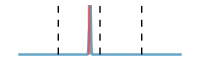
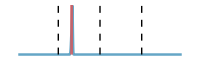
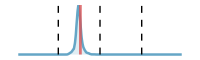
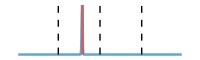
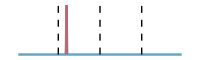
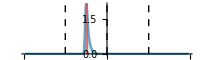
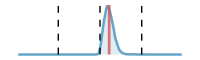
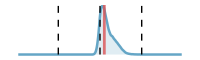
-Graphics-k_r^DP
-Graphics-k_h
-Graphics-k_a
-Graphics-k_b
-Graphics-k_p
-Graphics-k_dBasic parameters | -Graphics-Δk_TP^(A, T)
-Graphics-Δk_TP^(A, S)
-Graphics-Δk_TP^(A, D)Nuc. exch. (A&P) | -Graphics-Δk_h^T
-Graphics-Δk_h^S
-Graphics-Δk_h^DHydrolysis (P) | -Graphics-Δk_h^(A, T)
-Graphics-Δk_h^(A, S)
-Graphics-Δk_h^(A, D)
-Graphics-Δk_h^(A, U)Hydrolysis (A&P)
-Graphics-Δk_a^(U, DP)
-Graphics-δk_a^(T, DP)
-Graphics-δk_a^(S, DP)
-Graphics-Δk_a^(D, DP)
-Graphics-δk_a^(T, TP)
-Graphics-δk_a^(S, TP)
-Graphics-δk_a^(D, TP)KaiA on (N&P) | -Graphics-Δk_b^(U, DP)
-Graphics-Δk_b^(T, DP)
-Graphics-Δk_b^(S, DP)
-Graphics-Δk_b^(D, DP)
-Graphics-Δk_b^(T, TP)
-Graphics-Δk_b^(S, TP)
-Graphics-Δk_b^(D, TP)KaiA off (N&P) | -Graphics-Δk_p^US
-Graphics-Δk_d^SU
-Graphics-Δk_p^TD
-Graphics-Δk_d^DT
-Graphics-Δk_p^SD
-Graphics-Δk_d^DS(De)phos. (P) | -Graphics-Δk_p^(A, US)
-Graphics-Δk_d^(A, SU)
-Graphics-Δk_p^(A, TD)
-Graphics-Δk_d^(A, DT)
-Graphics-Δk_p^(A, SD)
-Graphics-Δk_d^(A, DS)
-Graphics-Δk_p^(A, UT)
-Graphics-Δk_d^(A, TU)(De)phos. (A&P)

```mathematica
posteriors=Grid[{{distr1,distr2,distr3,distr4},{distr5,distr6,distr7,distr8}},Alignment->Top]
```

## Posterior plot (independent-rate scheme)

```mathematica
pltNamesReparam={"Hydrolysis","Hydrolysis (KaiA)","(De)phos.","(De)phos. (KaiA)","KaiA on","KaiA off","Nuc. exch."};
```

```mathematica
allParamLstReparam={{"k_h^U","k_h^T","k_h^S","k_h^D"},
{"k_h^(A, U)","k_h^(A, T)","k_h^(A, S)","k_h^(A, D)"},
{"k_p^UT","k_d^TU","k_p^US","k_d^SU","k_p^TD","k_d^DT","k_p^SD","k_d^DS"},
{"k_p^(A, UT)","k_d^(A, TU)","k_p^(A, US)","k_d^(A, SU)","k_p^(A, TD)","k_d^(A, DT)","k_p^(A, SD)","k_d^(A, DS)"},
{"k_a^(U, TP)","k_a^(U, DP)","k_a^(T, TP)","k_a^(T, DP)","k_a^(S, TP)","k_a^(S, DP)","k_a^(D, TP)","k_a^(D, DP)"},
{"k_b^(U, TP)","k_b^(U, DP)","k_b^(T, TP)","k_b^(T, DP)","k_b^(S, TP)","k_b^(S, DP)","k_b^(D, TP)","k_b^(D, DP)"},
{"k_r^(DP, U)","k_r^(DP, T)","k_r^(DP, S)","k_r^(DP, D)"}};
allParamLstParamFlat=Flatten[allParamLstReparam];
```

```mathematica
allParamReparam[walker_]:=Module[{krD,kh,ka,kb,kp,kd,dkT,dkD,dkDT,dkhT,dkhS,dkTAD,dkbSDP,dkbDDP,dkbTTP,dkbDTP,dkdSU,dkpTD,dkdDT,dkpSD,dkdATU,dkdADT,dkpAUS,dkDS,dkTD,dkDD,dkhD,dkTAT,dkDAT,dkTAS,dkDAS,dkDAD,dkhAU,dkhAT,dkhAS,dkhAD,dkbUDP,dkbTDP,dkbSTP,dkdDS,dkpASD,dkdADS,dkpAUT,dkpATD,dkdASU,dkaDDP,kTA,kDA,kT,kD,dkaSTP,dkaTTP,dkaTDP,dkaSDP,dkaUDP,dkaDTP,dkTT,dkTS,dkpUS},

(*Define the free parameters and assign their values*)
{krD,kh,ka,kb,kp,kd,dkhT,dkhS,dkhD,dkTAT,dkTAS,dkTAD,dkhAU,dkhAT,dkhAS,dkhAD,dkaUDP,dkbUDP,dkbTDP,dkbSDP,dkaDDP,dkbDDP,dkbTTP,dkbSTP,dkaDTP,dkbDTP,dkpUS,dkdSU,dkpTD,dkdDT,dkpSD,dkdDS,dkpAUT,dkdATU,dkpATD,dkdADT,dkpASD,dkdADS,dkpAUS,dkdASU}=walker⟦1;;nFreePar-1⟧;

kTA=krD;

dkaSTP=(dkbSTP+dkaDDP+dkdADS)-(dkbDDP+dkpASD);
dkaTTP=(dkbTTP+dkaDDP+dkdADT)-(dkbDDP+dkpATD);
dkaTDP=(dkbTDP+dkpAUT)-dkdATU;
dkaSDP=(dkbSDP+dkpAUS)-dkdASU;

{kh,kh+dkhT,kh+dkhS,kh+dkhD,
kh+dkhAU,kh+dkhT+dkhAT,kh+dkhS+dkhAS,kh+dkhD+dkhAD,
kp,kd,kp+dkpUS,kd+dkdSU,kp+dkpTD,kd+dkdDT,kp+dkpSD,kd+dkdDS,
kp+dkpAUT,kd+dkdATU,kp+dkpUS+dkpAUS,kd+dkdSU+dkdASU,kp+dkpTD+dkpATD,kd+dkdDT+dkdADT,kp+dkpSD+dkpASD,kd+dkdDS+dkdADS,
ka,ka+dkaUDP,ka+dkaTTP,ka+dkaTDP,ka+dkaSTP,ka+dkaSDP,ka+dkaDTP,ka+dkaDDP,
kb,kb+dkbUDP,kb+dkbTTP,kb+dkbTDP,kb+dkbSTP,kb+dkbSDP,kb+dkbDTP,kb+dkbDDP,
kTA,kTA+dkTAT,kTA+dkTAS,kTA+dkTAD}
]
```

```mathematica
iterTrajFlatAllParamReparam=allParamReparam[#]&/@iterTrajFlat;
```

```mathematica
bestWalkerAllParamReparam=allParamReparam[bestWalker];
```

```mathematica
allParamReparamPartition={{1,4},{5,8},{9,16},{17,24},{25,32},{33,40},{41,44}};
```

```mathematica
grayLevel=0.35;
minorFont=20;
majorFont=25;
distrColor=ColorData["DarkBands"][0.1];
distrColor2=ColorData["DarkBands"][0.2];
distrColor3=ColorData["DarkBands"][0.5];
lineColor=ColorData["CherryTones"][0.5];
thickness=0.009;
font="Arial";

{distr1Reparam,distr2Reparam,distr3Reparam,distr4Reparam,distr5Reparam,distr6Reparam,distr7Reparam}=Table[
Labeled[Column[
Table[
Labeled[
Overlay[{
SmoothHistogram[iterTrajFlatAllParamReparam⟦All,i⟧,Automatic,"PDF",AspectRatio->0.3,PlotStyle->{Thickness[thickness],distrColor},Filling->Axis,AxesStyle->Directive[Black],ImageSize->200,PlotRange->{{-9.8,9.8},All},BaseStyle->FontSize->minorFont,If[i==allParamReparamPartition⟦cat,2⟧,Axes->{True,False},Axes->False],Epilog->{{lineColor,Thickness[0.01],Opacity[0.8],Line[{{bestWalkerAllParamReparam⟦i⟧,0},{bestWalkerAllParamReparam⟦i⟧,100}}]},{Black,Thickness[0.005],Dashed,Line[{{-5,0},{-5,100}}],Line[{{0,0},{0,100}}],Line[{{5,0},{5,100}}]}}]}]
,Style[allParamLstReparam⟦cat,i-allParamReparamPartition⟦cat,1⟧+1⟧,minorFont,Black,FontFamily->font],Left],
{i,allParamReparamPartition⟦cat,1⟧,allParamReparamPartition⟦cat,2⟧}],
Alignment->Right
],Style[pltNamesReparam⟦cat⟧,minorFont,GrayLevel[grayLevel],Black,FontFamily->font],Top]
,{cat,7}];
```

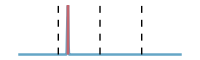
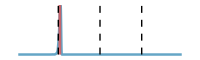
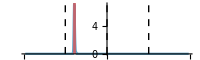
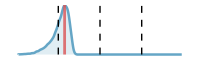
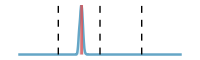
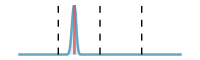
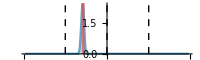
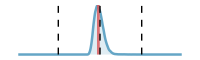
-Graphics-k_h^U
-Graphics-k_h^T
-Graphics-k_h^S
-Graphics-k_h^DHydrolysis | -Graphics-k_h^(A, U)
-Graphics-k_h^(A, T)
-Graphics-k_h^(A, S)
-Graphics-k_h^(A, D)Hydrolysis (KaiA) | -Graphics-k_r^(DP, U)
-Graphics-k_r^(DP, T)
-Graphics-k_r^(DP, S)
-Graphics-k_r^(DP, D)Nuc. exch. | 
-Graphics-k_p^UT
-Graphics-k_d^TU
-Graphics-k_p^US
-Graphics-k_d^SU
-Graphics-k_p^TD
-Graphics-k_d^DT
-Graphics-k_p^SD
-Graphics-k_d^DS(De)phos. | -Graphics-k_p^(A, UT)
-Graphics-k_d^(A, TU)
-Graphics-k_p^(A, US)
-Graphics-k_d^(A, SU)
-Graphics-k_p^(A, TD)
-Graphics-k_d^(A, DT)
-Graphics-k_p^(A, SD)
-Graphics-k_d^(A, DS)(De)phos. (KaiA) | -Graphics-k_a^(U, TP)
-Graphics-k_a^(U, DP)
-Graphics-k_a^(T, TP)
-Graphics-k_a^(T, DP)
-Graphics-k_a^(S, TP)
-Graphics-k_a^(S, DP)
-Graphics-k_a^(D, TP)
-Graphics-k_a^(D, DP)KaiA on | -Graphics-k_b^(U, TP)
-Graphics-k_b^(U, DP)
-Graphics-k_b^(T, TP)
-Graphics-k_b^(T, DP)
-Graphics-k_b^(S, TP)
-Graphics-k_b^(S, DP)
-Graphics-k_b^(D, TP)
-Graphics-k_b^(D, DP)KaiA off

```mathematica
posteriorsReparam=Grid[{{distr1Reparam,distr2Reparam,distr7Reparam},{distr3Reparam,distr4Reparam,distr5Reparam,distr6Reparam}},Alignment->Top]
```

## Posteriors for initial conditions and global variance

```mathematica
initCondNames={"[C_TP^U]_0","[C_DP^U]_0","[C_TP^T]_0","[C_DP^T]_0","[C_TP^S]_0","[C_DP^S]_0","[C_TP^D]_0","[C_DP^D]_0","σ"};
```

```mathematica
initConds[walker_]:=Module[{σ2,CUTP,CUDP,CTTP,CTDP,CSTP,CSDP,CDTP,CDDP},

(*Define the free parameters and assign their values*)
{σ2,CUTP,CUDP,CTTP,CTDP,CSTP,CSDP,CDTP}=walker⟦nFreePar;;-1⟧;
CDDP=3.5-CUTP-CUDP-CTTP-CTDP-CSTP-CSDP-CDTP;
{CUTP,CUDP,CTTP,CTDP,CSTP,CSDP,CDTP,CDDP,σ2^(1/2)}
]
```

```mathematica
initCondsBestWalker=initConds[bestWalker];
```

```mathematica
initCondsAll=initConds[#]&/@iterTrajFlat;
```

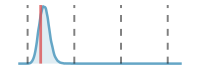
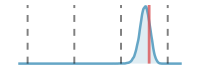
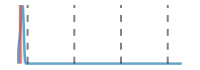
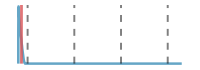
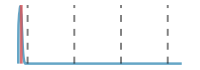
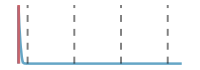
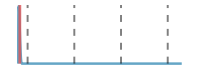
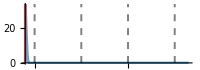
-Graphics-[C_TP^U]_0
-Graphics-[C_DP^U]_0
-Graphics-[C_TP^T]_0
-Graphics-[C_DP^T]_0
-Graphics-[C_TP^S]_0
-Graphics-[C_DP^S]_0
-Graphics-[C_TP^D]_0
-Graphics-[C_DP^D]_0Init. conds. (μM)

```mathematica
grayLevel=0.35;
minorFont=20;
majorFont=25;
distrColor=ColorData["DarkBands"][0.1];
distrColor2=ColorData["DarkBands"][0.2];
distrColor3=ColorData["DarkBands"][0.5];
lineColor=ColorData["CherryTones"][0.5];
thickness=0.009;
font="Arial";

initCondPlt=Labeled[Column[Table[Labeled[Overlay[{
SmoothHistogram[initCondsAll⟦All,i⟧,Automatic,"PDF",AspectRatio->0.35,PlotStyle->{Thickness[thickness],distrColor},Filling->Axis,AxesStyle->Directive[Black],Ticks->{{0.2,1.2,2.2,3.2},None},ImageSize->200,PlotRange->{{0,3.5},All},BaseStyle->FontSize->minorFont,If[i==8,Axes->{True,False},Axes->False],Epilog->{{lineColor,Thickness[0.01],Opacity[0.8],Line[{{initCondsBestWalker⟦i⟧,0},{initCondsBestWalker⟦i⟧,100}}]},{Black,Opacity[0.5],Thickness[0.007],Dashed,Line[{{0.2,0},{0.2,100}}],Line[{{1.2,0},{1.2,100}}],Line[{{2.2,0},{2.2,100}}],Line[{{3.2,0},{3.2,100}}]}}]}]
,Style[initCondNames⟦i⟧,minorFont,Black,FontFamily->font],Left],
{i,8}],
Alignment->Right],
Style["Init. conds. (μM)",Black,FontSize->minorFont,FontFamily->font],Top]
```

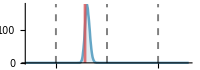
-Graphics-σGlobal error (μM)

```mathematica
errorPlt=Labeled[Labeled[Overlay[{
SmoothHistogram[initCondsAll⟦All,-1⟧,Automatic,"PDF",AspectRatio->0.35,PlotStyle->{Thickness[thickness],distrColor},Filling->Axis,AxesStyle->Directive[Black],Ticks->{{0.05,0.1,0.15},None},ImageSize->200,PlotRange->{{0.02,0.18},All},BaseStyle->FontSize->minorFont,Axes->{True,False},Epilog->{{lineColor,Thickness[0.01],Opacity[0.8],Line[{{initCondsBestWalker⟦-1⟧,0},{initCondsBestWalker⟦-1⟧,1000}}]},{Black,Opacity[0.5],Thickness[0.007],Dashed,Line[{{0.05,0},{0.05,1000}}],Line[{{0.1,0},{0.1,1000}}],Line[{{0.15,0},{0.15,1000}}]}}]}]
,Style[initCondNames⟦-1⟧,minorFont,Black,FontFamily->font],Left],
Style["Global error (μM)",Black,FontSize->minorFont,FontFamily->font],Top]
```

## Sensitivity/covariance analysis

```mathematica
distrMean=Mean[iterTrajFullFlat];
distrCentered=(#-distrMean)&/@iterTrajFullFlat;
```

```mathematica
covarMat=Table[Mean[distrCentered⟦All,i⟧distrCentered⟦All,j⟧],{i,Length[distrCentered⟦1⟧]},{j,Length[distrCentered⟦1⟧]}];
```

```mathematica
eigs=Eigensystem[covarMat];
```

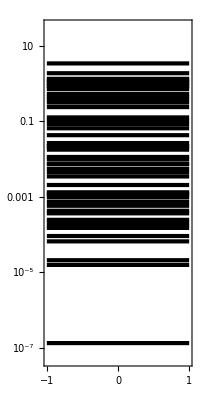

```mathematica
majorFont=30;
markerSize=10;
fts=({#,Superscript[10,ToString@Round@Log10[#]]}&)/@(10.^Range[-7,1,2]);
baseStyle={ImageSize->{200,400},AspectRatio->Full,PlotRange->{10^-7.3,10^1.5},Axes->False,BaseStyle->FontSize->majorFont,Frame->True,FrameTicks->{{None,fts},{None,None}},FrameStyle->Directive[Thick,Black],FrameTicksStyle->Thick,PlotStyle->{{Black,Thickness[0.015]}},FrameLabel->{None,"λ"}};

spectrum=Plot@@Flatten[{eigs⟦1⟧,{x,-1,1},ScalingFunctions->{Automatic,"Log"},baseStyle},{1}]
```

```mathematica
Proj=Diagonal[covarMat];
```

```mathematica
Intersections=1/Diagonal[Inverse[covarMat]];
```

```mathematica
ratio=Sort[√Abs[Intersections/Proj]];
```

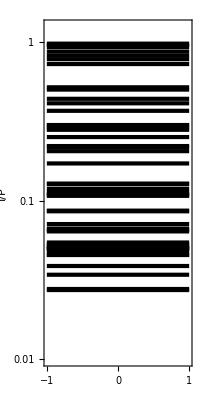

```mathematica
majorFont=30;
markerSize=10;
fts=({#,Superscript[10,ToString@Round@Log10[#]]}&)/@(10.^Range[-7,1,1]);
baseStyle={ImageSize->{200,400},AspectRatio->Full,PlotRange->{10^-2,10^0.1},Axes->False,BaseStyle->FontSize->majorFont,Frame->True,FrameTicks->{{None,fts},{None,None}},FrameStyle->Directive[Thick,Black],FrameTicksStyle->Thick,PlotStyle->{{Black,Thickness[0.015]}},FrameLabel->{None,"I/P"}};

alignment=Plot@@Flatten[{ratio,{x,-1,1},ScalingFunctions->{Automatic,"Log"},baseStyle},{1}]
```

## Autocorrelation time of the principal components

```mathematica
demean[traj_]:=traj-Mean[traj]
```

Automated windowing procedure following Sokal (1989)

```mathematica
autoWin[τs_]:=Module[{truePos,const},
const=5;
truePos=Flatten[Position[Positive[Range[0,Length[τs]-1]-const τs],True]];
If[Length[truePos]==0,Length[τs],truePos⟦1⟧]
]
```

```mathematica
meanACF[trajs_]:=Module[{demeanTraj,ACFs,len=600},
ACFs=Table[demeanTraj=demean[trajs⟦walker⟧];ListCorrelate[demeanTraj,demeanTraj,{1,1},0]/Range[Length[trajs⟦walker⟧],1.,-1.],{walker,Length[trajs]}];
Mean[ACFs]⟦1;;len⟧/Mean[ACFs⟦All,1⟧]
]
```

```mathematica
acor[meanACF_]:=Module[{taus},
taus=2Accumulate[meanACF]-1;
taus⟦autoWin[taus]⟧
]
```

```mathematica
iterTrajCentered=Table[iterTrajFull⟦walker,t⟧-distrMean,{walker,Length[iterTrajFull]},{t,Length[iterTrajFull⟦1⟧]}];
```

```mathematica
acors=Table[projection=Table[iterTrajCentered⟦walker,t⟧.eigs⟦2,pc⟧,{walker,Length[iterTrajFull]},{t,Length[iterTrajFull⟦1⟧]}];acor[meanACF[projection]],{pc,48}];
```

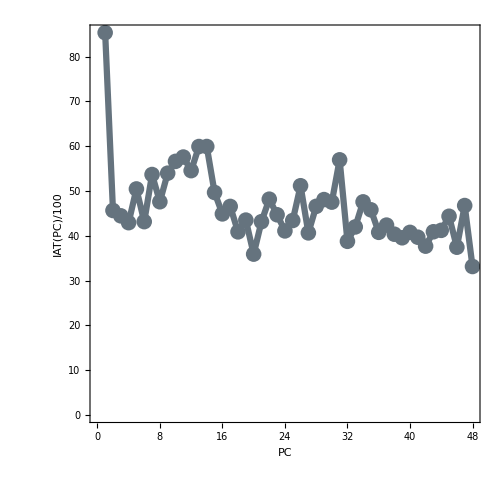

```mathematica
grayLevel=0.35;
minorFont=30;
majorFont=30;
markerSize=16;
thickness=0.009;
baseStyle={ImageSize->500,AspectRatio->1,PlotRange->All,BaseStyle->FontSize->majorFont,Axes->False,Frame->{{True,False},{True,False}},FrameStyle->Directive[Thick,Black],FrameTicksStyle->Thick,PlotMarkers->{Automatic,markerSize}};

iatPC=Show[
ListLinePlot[acors,baseStyle,PlotStyle->Table[{UTSDPfColorScheme⟦-1⟧,Thickness[thickness]},{i,{0,0.1,0.2,0.8,0.9,1}}],FrameLabel->{"PC","IAT(PC)/100"}]
]
```

# Comparison to Experiment

## Comparison to phosphorylation dataset

```mathematica
phosSol=Table[DoubleGeneral[bestWalker,ATPfrac,3.5,KaiA],{ATPfrac,{0.1,0.25,1.0}},{KaiA,{0.375,0.75,1.5,3.0,4.5,6.0}}];
```

```mathematica
pltTitle=Table[ATPfrac<>"% ATP, "<>KaiA<>" μM KaiA",{ATPfrac,{"10","25","100"}},{KaiA,{"0.38","0.75","1.50","3.00","4.50","6.00"}}];
```

```mathematica
grayLevel=0.35;
minorFont=15;
majorFont=30;
markerSize=14;
baseStyle={ImageSize->240,PlotRange->{{-1.5,13.5},{-10,110}},AspectRatio->1,BaseStyle->FontSize->majorFont,Frame->True,Axes->False,FrameTicks->{{{10,50,90},False},{{0,4,8,12},False}},FrameStyle->Directive[Thick,Black],FrameTicksStyle->Thick,PlotStyle->{Table[Thickness[0.015],{i,0,3}],UTSDPfColorScheme⟦1;;4⟧}ᵀ};

phosphoFit=Flatten@Table[Plot@@Flatten[{Table[Plus@@phosSol⟦ATPfrac,KaiA,phosForm⟧,{phosForm,{UKaiC,TKaiC,SKaiC,DKaiC}}],{t,0,12.5},baseStyle},{1}],{ATPfrac,3},{KaiA,6}];

phosphoData=Table[ListPlot[Table[{phosData⟦rxn,All,1⟧,phosData⟦rxn,All,phosForm⟧}ᵀ,{phosForm,{5,3,4,2}}],Axes->False,ImageSize->250,PlotRange->{-10,100},PlotStyle->UTSDPfColorScheme⟦1;;4⟧,PlotMarkers->{Automatic,markerSize}],{rxn,{3,6,9,12,15,18,2,5,8,11,14,17,1,4,7,10,13,16}}];
```

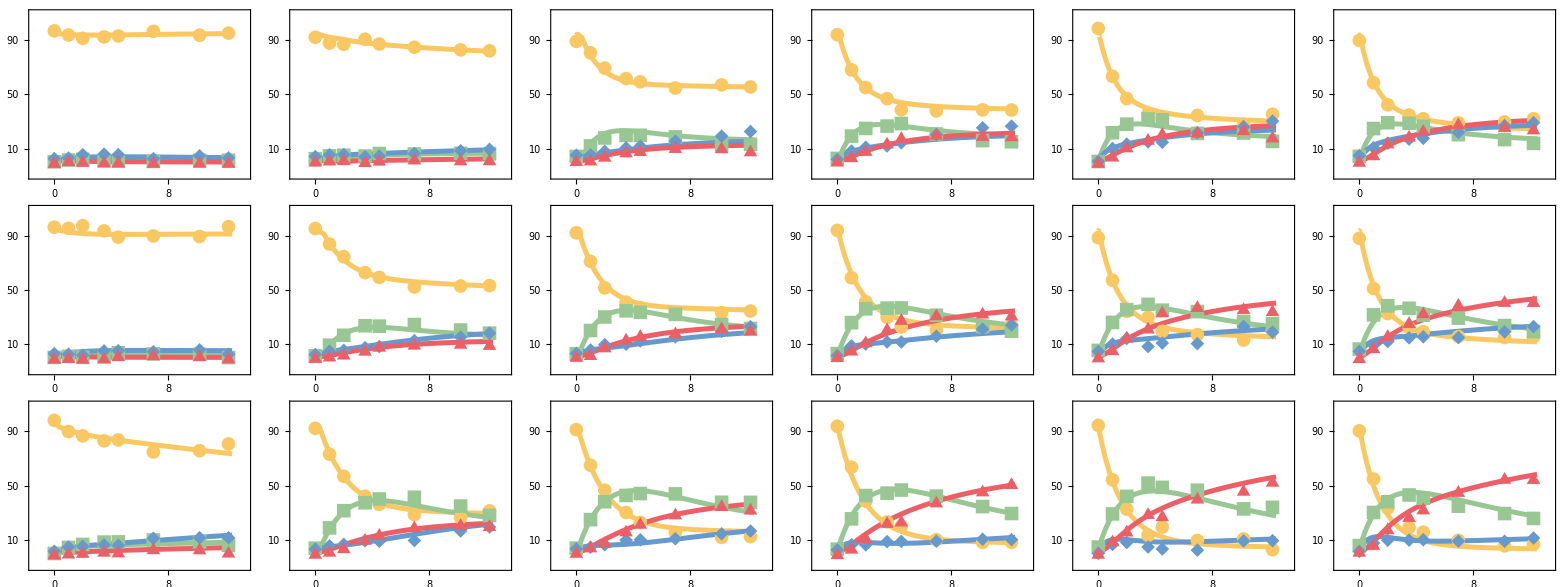

```mathematica
phosGridPlt=Grid[Partition[Table[Show[phosphoFit⟦i⟧,phosphoData⟦i⟧],{i,Length[phosphoFit]}],6]]
```

## Comparison to dephos. data

For the dephos rxn, [KaiC] = 3.4, [KaiA] = 1.3, and ATPfrac = 1.0

```mathematica
dephosSol=DoubleGeneralDephos[bestWalker,1.0,1.0,3.4,1.3];
```

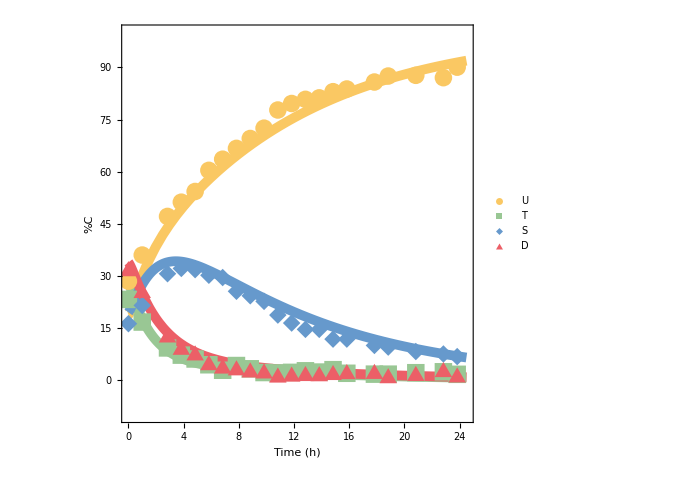

```mathematica
minorFont=35;
majorFont=35;
markerSize=18;
baseStyle={ImageSize->500,AspectRatio->1,PlotRange->{-10,100},BaseStyle->FontSize->majorFont,Frame->{{True,False},{True,False}},FrameStyle->Directive[Thick,Black],FrameTicksStyle->Thick,PlotStyle->{Table[Thickness[0.014],{i,0,3}],UTSDPfColorScheme⟦1;;4⟧}ᵀ,FrameLabel->{"Time (h)"}};

dephosPlt=Show[Plot@@Flatten[{Table[Plus@@dephosSol⟦phosForm⟧,{phosForm,{UKaiC,TKaiC,SKaiC,DKaiC}}],{t,0,24.5},FrameLabel->{"Time (h)",Style["%C",SingleLetterItalics->False]},baseStyle},{1}],
ListPlot[dephosData,PlotStyle->UTSDPfColorScheme⟦1;;4⟧,PlotMarkers->{Automatic,markerSize},PlotLegends->Placed[LineLegend[Automatic,Style[#,minorFont,Black]&/@{"U","T","S","D"},Spacings->0.1,LegendMarkerSize->markerSize],{0.9,0.5}]]]
```

## Comparison to KaiC hydrolysis rate measurements

```mathematica
phosPiSol=Table[DoubleGeneralPi[bestWalker,ATPfrac,3.5,KaiA]⟦-1⟧,{ATPfrac,{0.1,0.25,1.0}},{KaiA,{0.375,0.75,1.5,3.0,4.5,6.0}}]/3.5;
```

```mathematica
PiBound=Plot[{1.16t,1.22t},{t,0,13},PlotStyle->Gray,Filling->{1->{2}}];
PiTerauchiBound=Plot[{0.6t,1.24t},{t,0,13},PlotStyle->White,Filling->{1->{2}},FillingStyle->{Gray,Opacity[0.8]}];
```

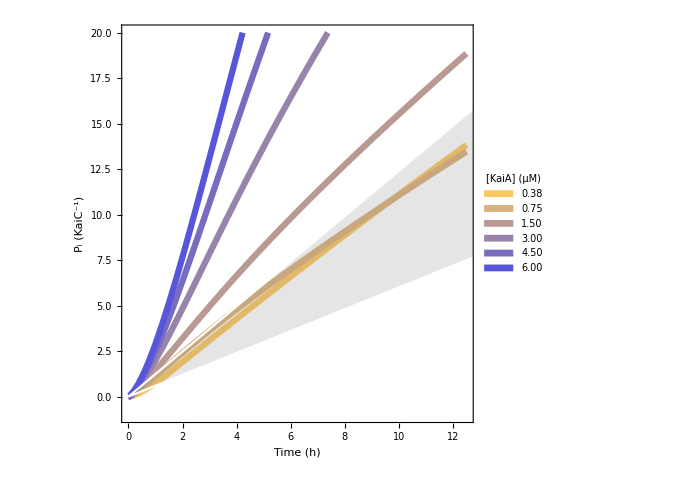

```mathematica
grayLevel=0.35;
minorFont=35;
majorFont=35;
colorScheme=Table[Blend[{UTSDPfColorScheme⟦1⟧,UTSDPfColorScheme⟦5⟧},i/5.],{i,0,5}];
markerSize=20;
baseStyle={ImageSize->500,Axes->False,AspectRatio->1,PlotRange->{-1,20},BaseStyle->FontSize->majorFont,Frame->{{True,False},{True,False}},FrameStyle->Directive[Thick,Black],FrameTicksStyle->Thick,PlotStyle->{Table[Thickness[0.009],{i,0,5}],colorScheme}ᵀ,FrameLabel->{"Time (h)",Style["P_i (KaiC^-1)",SingleLetterItalics->False]}};
HydroPlt=Show[Plot@@Flatten[{Table[phosPiSol⟦3,KaiA⟧,{KaiA,6}],{t,0,12.5},baseStyle,PlotLegends->Placed[SwatchLegend[Automatic,Style[#,minorFont,Black]&/@{"0.38","0.75","1.50","3.00","4.50","6.00"},Spacings->0.1,LegendMarkerSize->markerSize,LegendLabel->Style["[KaiA]\n(μM)\n",minorFont,Black]],Right]},{1}],PiTerauchiBound]
```

## Comparison to KaiA dwell time measurement

```mathematica
dissociation[walker_]:=Module[{krT,krD,Kon,kh,ka,kb,kp,kd,dkT,dkD,dkDT,dkhT,dkhS,dkTAD,dkbSDP,dkbDDP,dkbTTP,dkbDTP,dkdSU,dkpTD,dkdDT,dkpSD,dkdATU,dkdADT,dkpAUS,dkDS,dkTD,dkDD,dkhD,dkTAT,dkDAT,dkTAS,dkDAS,dkDAD,dkhAU,dkhAT,dkhAS,dkhAD,dkbUDP,dkbTDP,dkbSTP,dkdDS,dkpASD,dkdADS, dkpAUT, dkpATD,dkdASU,dkaDDP,nucTotal,ATP,ADP,ATPWeighedFrac,kTA,kDA,kT,kD,dkaSTP,dkaTTP,dkaTDP,dkaSDP,dkaUDP,dkaDTP,dkTT,dkTS,dkpUS,UT,TD,SU,DS,aUT,aTD,aSU,aDS,nuctot,ATPweighedfrac},

(*Define the free parameters and assign their values*)
{krD,kh,ka,kb,kp,kd,dkhT,dkhS,dkhD,dkTAT,dkTAS,dkTAD,dkhAU,dkhAT,dkhAS,dkhAD,dkaUDP,dkbUDP,dkbTDP,dkbSDP,dkaDDP,dkbDDP,dkbTTP,dkbSTP,dkaDTP,dkbDTP,dkpUS,dkdSU,dkpTD,dkdDT,dkpSD,dkdDS,dkpAUT,dkdATU,dkpATD,dkdADT,dkpASD,dkdADS,dkpAUS,dkdASU}=10^walker⟦1;;nFreePar-1⟧;

Kon=1;
nuctot=5000.;
ATP=0.5*nuctot;
ADP=nuctot-ATP;
ATPweighedfrac=ATP/(ATP+Kon*ADP);
kTA=krD*ATPweighedfrac;
dkaSTP=(dkbSTP*dkaDDP*dkdADS)/(dkbDDP*dkpASD);
dkaTTP=(dkbTTP*dkaDDP*dkdADT)/(dkbDDP*dkpATD);
dkaTDP=(dkbTDP*dkpAUT)/dkdATU;
dkaSDP=(dkbSDP*dkpAUS)/dkdASU;

{ka,kb,kb dkbUDP,kb dkbTTP,kb dkbTDP,kb dkbSTP,kb dkbSDP,kb dkbDTP,kb dkbDDP}
]
```

```mathematica
dwellTime=Join[{dissociation[bestWalker]⟦1⟧},1/dissociation[bestWalker]⟦2;;-1⟧];
```

```mathematica
dwellTimeAll=Join[{dissociation[#]⟦1⟧},1/dissociation[#]⟦2;;-1⟧]&/@iterTrajFlat;
```

```mathematica
dwellTimeAllErrors=Table[{Quantile[dwellTimeAll⟦All,i⟧,0.025],Quantile[dwellTimeAll⟦All,i⟧,1-0.025]},{i,9}];
```

```mathematica
kaExp=0.0279;τUexp=1/0.0663;τTexp=1.;τSexp=0.43;τDexp=0.26;
```

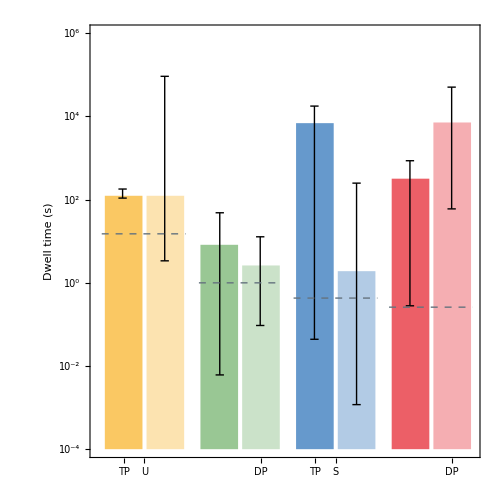

```mathematica
grayLevel=0.35;
minorFont=30;
majorFont=30;
markerSize=20;
baseStyle={ImageSize->500,AspectRatio->1,PlotRange->{10^-4,10^6},BaseStyle->FontSize->majorFont,Frame->{{True,False},{True,False}},FrameStyle->Directive[Thick,Black],FrameTicksStyle->Thick,FrameLabel->{None,"Dwell time (s)"},ChartStyle->{UTSDPfColorScheme⟦1;;4⟧,{Opacity[1],Opacity[0.5]}},ChartBaseStyle->EdgeForm[]};
fts=({#,Superscript[10,ToString@Round@Log10[#]]}&)/@(10.^Range[-4,8,2]);
lineColor=UTSDPfColorScheme⟦-1⟧;

barPosition={Indeterminate,1.17,2.18,3.5,4.47,5.77,6.78,8.06,9.06};
barWidth=0.1;
errorBars=Table[{Line[{{barPosition⟦i⟧,Log[10,dwellTimeAllErrors⟦i,1⟧]},{barPosition⟦i⟧,Log[10,dwellTimeAllErrors⟦i,2⟧]}}],Line[{{barPosition⟦i⟧-barWidth,Log[10,dwellTimeAllErrors⟦i,1⟧]},{barPosition⟦i⟧+barWidth,Log[10,dwellTimeAllErrors⟦i,1⟧]}}],Line[{{barPosition⟦i⟧-barWidth,Log[10,dwellTimeAllErrors⟦i,2⟧]},{barPosition⟦i⟧+barWidth,Log[10,dwellTimeAllErrors⟦i,2⟧]}}]},{i,2,9}];

expBars={Line[{{barPosition⟦2⟧-0.5,Log[10,τUexp]},{barPosition⟦3⟧+0.5,Log[10,τUexp]}}],
Line[{{barPosition⟦4⟧-0.5,Log[10,τTexp]},{barPosition⟦5⟧+0.5,Log[10,τTexp]}}],
Line[{{barPosition⟦6⟧-0.5,Log[10,τSexp]},{barPosition⟦7⟧+0.5,Log[10,τSexp]}}],
Line[{{barPosition⟦8⟧-0.5,Log[10,τDexp]},{barPosition⟦9⟧+0.5,Log[10,τDexp]}}]};

dwellTimePlt=Show[
BarChart[Partition[dwellTime⟦2;;9⟧,2],baseStyle,ScalingFunctions->"Log10",FrameTicks->{Automatic,fts},ChartLabels->{{"U","T","S","D"},{"TP","DP"}}],
Graphics[{Thick,Black,errorBars}],
Graphics[{Thick,lineColor,Dashed,expBars}]
]
```

# Model analysis

## KaiAC state kinetics

## utility functions

```mathematica
DoubleGeneralPathConc[walker_,ATPfrac_,KaiC_,KaiA_,block_:"none",time_:12]:=Module[
{secToHour=3600,
initInd={1,2,3,4,9,10,11,12}(*the last concentration needs to be calculated manually*)},

(*Define state variables and their initial conditions*)
(*stateVars={CTu,CDu,CTt,CDt,ACTu,ACDu,ACTt,ACDt,CTs,CDs,CTd,CDd,ACTs,ACDs,ACTd,ACDd,A};
initConds=ConstantArray[0,Length[stateVars]];
initConds⟦2⟧=KaiC;
initConds⟦-1⟧=KaiA/2;*)

stateVars={CTu,CDu,CTt,CDt,ACTu,ACDu,ACTt,ACDt,CTs,CDs,CTd,CDd,ACTs,ACDs,ACTd,ACDd,A};
initConds=ConstantArray[0,Length[stateVars]];
initConds⟦initInd⟦1;;-2⟧⟧=walker⟦nFreePar+1;;-1⟧;
initConds⟦initInd⟦-1⟧⟧=3.5-Total[walker⟦nFreePar+1;;-1⟧];
initConds⟦initInd⟧=KaiC/3.5 initConds⟦initInd⟧;(*scale the initial condition; this is importance since the fitting assumption is that total KaiC is 3.5 uM*)
initConds⟦-1⟧=KaiA/2;

(*Define the free parameters and assign their values*)
{krD,kh,ka,kb,kp,kd,dkhT,dkhS,dkhD,dkTAT,dkTAS,dkTAD,dkhAU,dkhAT,dkhAS,dkhAD,dkaUDP,dkbUDP,dkbTDP,dkbSDP,dkaDDP,dkbDDP,dkbTTP,dkbSTP,dkaDTP,dkbDTP,dkpUS,dkdSU,dkpTD,dkdDT,dkpSD,dkdDS,dkpAUT,dkdATU,dkpATD,dkdADT,dkpASD,dkdADS,dkpAUS,dkdASU}=10^walker⟦1;;nFreePar-1⟧;

Kon=1;
nuctot=5000.;
ATP=ATPfrac*nuctot;
ADP=nuctot-ATP;
ATPweighedfrac=ATP/(ATP+Kon*ADP);
kTA=krD*ATPweighedfrac;
dkaSTP=(dkbSTP*dkaDDP*dkdADS)/(dkbDDP*dkpASD);
dkaTTP=(dkbTTP*dkaDDP*dkdADT)/(dkbDDP*dkpATD);
dkaTDP=(dkbTDP*dkpAUT)/dkdATU;
dkaSDP=(dkbSDP*dkpAUS)/dkdASU;

flux0t1=kh;
flux0t3=kp;
flux0t4=ka;
flux0t9=kp dkpUS;
flux1t5=ka dkaUDP;
flux2t3=kh dkhT;
flux2t6=ka dkaTTP;
flux2t11=kp dkpTD;
flux3t0=kd;
flux3t7=ka dkaTDP;
flux4t0=kb;
flux4t5=kh dkhAU;
flux4t7=kp dkpAUT;
flux4t13=kp dkpUS dkpAUS;
flux5t1=kb dkbUDP;
flux5t4=kTA;
flux6t2=kb dkbTTP;
flux6t7=kh dkhT dkhAT;
flux6t15=kp dkpTD dkpATD;
flux7t3=kb dkbTDP;
flux7t4=kd dkdATU;
flux7t6=kTA dkTAT;
flux8t9=kh dkhS;
flux8t11=kp dkpSD;
flux8t12=ka dkaSTP;
flux9t0=kd dkdSU;
flux9t13=ka dkaSDP;
flux10t11=kh dkhD;
flux10t14=ka dkaDTP;
flux11t2=kd dkdDT;
flux11t8=kd dkdDS;
flux11t15=ka dkaDDP;
flux12t8=kb dkbSTP;
flux12t13=kh dkhS dkhAS;
flux12t15=kp dkpSD dkpASD;
flux13t4=kd dkdSU dkdASU;
flux13t9=kb dkbSDP;
flux13t12=kTA dkTAS;
flux14t10=kb dkbDTP;
flux14t15=kh dkhD dkhAD;
flux15t6=kd dkdDT dkdADT;
flux15t11=kb dkbDDP;
flux15t12=kd dkdDS dkdADS;
flux15t14=kTA dkTAD;

Switch[block,
"S",flux0t9=flux9t0=flux4t13=flux13t4=flux2t11=flux11t2=flux6t15=flux15t6=0,
"T",flux0t3=flux3t0=flux4t7=flux7t4=flux8t11=flux11t8=flux12t15=flux15t12=0,
"both",flux0t3=flux3t0=flux0t9=flux9t0=flux4t7=flux7t4=flux4t13=flux13t4=0,
"none",Null];

(*Solve the ODE; note that the resulting solutions are in hour*)
sol=Through[stateVars[t]]/.
Flatten[
NDSolve[Flatten[{stateVars[[1]]'[t]==-(flux0t1+flux0t4 A[t]+flux0t9+flux0t3)stateVars[[1]][t]+flux3t0 stateVars[[4]][t]+flux4t0 stateVars[[5]][t]+flux9t0 stateVars[[10]][t],stateVars[[2]]'[t]==flux0t1 stateVars[[1]][t]-flux1t5 A[t]stateVars[[2]][t]+flux5t1 stateVars[[6]][t],
stateVars[[3]]'[t]==-(flux2t3+flux2t6 A[t]+flux2t11)stateVars[[3]][t]+flux6t2 stateVars[[7]][t]+flux11t2 stateVars[[12]][t],stateVars[[4]]'[t]==flux0t3 stateVars[[1]][t]+flux2t3 stateVars[[3]][t]-(flux3t0+flux3t7 A[t])stateVars[[4]][t]+flux7t3 stateVars[[8]][t],stateVars[[5]]'[t]==flux0t4 A[t]stateVars[[1]][t]-(flux4t0+flux4t5+flux4t13+flux4t7)stateVars[[5]][t]+flux5t4 stateVars[[6]][t]+flux7t4 stateVars[[8]][t]+flux13t4 stateVars[[14]][t],stateVars[[6]]'[t]==flux1t5 A[t]stateVars[[2]][t]+flux4t5 stateVars[[5]][t]-(flux5t1+flux5t4)stateVars[[6]][t],stateVars[[7]]'[t]==flux2t6 A[t]stateVars[[3]][t]-(flux6t2+flux6t7+flux6t15)stateVars[[7]][t]+flux7t6 stateVars[[8]][t]+flux15t6 stateVars[[16]][t],
stateVars[[8]]'[t]==flux3t7 A[t]stateVars[[4]][t]+flux4t7 stateVars[[5]][t]+flux6t7 stateVars[[7]][t]-(flux7t3+flux7t4+flux7t6)stateVars[[8]][t],stateVars[[9]]'[t]==-(flux8t9+flux8t12 A[t]+flux8t11)stateVars[[9]][t]+flux11t8 stateVars[[12]][t]+flux12t8 stateVars[[13]][t],stateVars[[10]]'[t]==flux0t9 stateVars[[1]][t]+flux8t9 stateVars[[9]][t]-(flux9t0+flux9t13 A[t])stateVars[[10]][t]+flux13t9 stateVars[[14]][t],stateVars[[11]]'[t]==-(flux10t11+flux10t14 A[t])stateVars[[11]][t]+flux14t10 stateVars[[15]][t],
stateVars[[12]]'[t]==flux2t11 stateVars[[3]][t]+flux8t11 stateVars[[9]][t]+flux10t11 stateVars[[11]][t]-(flux11t2+flux11t8+flux11t15 A[t])stateVars[[12]][t]+flux15t11 stateVars[[16]][t],
stateVars[[13]]'[t]==flux8t12 A[t]*stateVars[[9]][t]-(flux12t8+flux12t13+flux12t15)stateVars[[13]][t]+flux13t12 stateVars[[14]][t]+flux15t12 stateVars[[16]][t],
stateVars[[14]]'[t]==flux4t13 stateVars[[5]][t]+flux9t13 A[t]stateVars[[10]][t]+flux12t13 stateVars[[13]][t]-(flux13t9+flux13t4+flux13t12)stateVars[[14]][t],stateVars[[15]]'[t]==flux10t14 A[t]stateVars[[11]][t]-(flux14t10+flux14t15)stateVars[[15]][t]+flux15t14 stateVars[[16]][t],stateVars[[16]]'[t]==flux6t15 stateVars[[7]][t]+flux11t15 A[t]stateVars[[12]][t]+flux12t15 stateVars[[13]][t]+flux14t15 stateVars[[15]][t]-(flux15t11+flux15t6+flux15t12+flux15t14)stateVars[[16]][t],
stateVars[[17]]'[t]==-flux0t4 A[t]stateVars[[1]][t]-flux1t5 A[t]stateVars[[2]][t]-flux2t6 A[t]stateVars[[3]][t]-flux3t7 A[t]stateVars[[4]][t]+flux4t0 stateVars[[5]][t]+flux5t1 stateVars[[6]][t]+flux6t2 stateVars[[7]][t]+flux7t3 stateVars[[8]][t]-flux8t12 A[t]stateVars[[9]][t]-flux9t13 A[t]stateVars[[10]][t]-flux10t14 A[t]stateVars[[11]][t]-flux11t15 A[t]stateVars[[12]][t]+flux12t8 stateVars[[13]][t]+flux13t9 stateVars[[14]][t]+flux14t10 stateVars[[15]][t]+flux15t11 stateVars[[16]][t],

Table[stateVars⟦i⟧[0]==initConds⟦i⟧,{i,Length[initConds]}]}],
Through[stateVars[t]],{t,0,time secToHour}]
]/.t->secToHour t;
sol
]
```

## KaiC phosphorylation state kinetics

```mathematica
time=Range[0,12,0.005];
```

```mathematica
solBestWalker=DoubleGeneral[bestWalker,1.0,3.5,1.5,12]⟦{2,6,5,1,4,8,7,3,10,14,13,9,12,16,15,11,17}⟧/.t->time;
sols=Quiet@ParallelTable[Check[DoubleGeneral[walker,1.0,3.5,1.5,12]⟦{2,6,5,1,4,8,7,3,10,14,13,9,12,16,15,11,17}⟧/.t->time,∞],{walker,iterTrajFlat⟦;;;;100⟧}];
sols=DeleteCases[sols,∞];
solCI=ParallelTable[{Quantile[sols⟦All,species,t⟧,0.025],Quantile[sols⟦All,species,t⟧,1-0.025]},{species,17},{t,Length[sols⟦1,1⟧]}];
```

```mathematica
solBestWalkerLowA=DoubleGeneral[bestWalker,1.0,3.5,0.2,12]⟦{2,6,5,1,4,8,7,3,10,14,13,9,12,16,15,11,17}⟧/.t->time;
solsLowA=Quiet@ParallelTable[Check[DoubleGeneral[walker,1.0,3.5,0.2,12]⟦{2,6,5,1,4,8,7,3,10,14,13,9,12,16,15,11,17}⟧/.t->time,∞],{walker,iterTrajFlat⟦;;;;100⟧}];
solsLowA=DeleteCases[solsLowA,∞];
solCILowA=ParallelTable[{Quantile[solsLowA⟦All,species,t⟧,0.025],Quantile[solsLowA⟦All,species,t⟧,1-0.025]},{species,17},{t,Length[solsLowA⟦1,1⟧]}];
```

```mathematica
minorFont=30;
majorFont=30;
markerSize=18;
thickness=4;
baseStyle={PlotRange->All,AspectRatio->Full,BaseStyle->FontSize->majorFont,Frame->True,Axes->False,FrameStyle->Directive[Thick,Black],FrameTicksStyle->Thick};

plot[species_,plotRange_,phosphoform_,ticks_:{0,40,80}]:=Show[
ListLinePlot[{{time,solCILowA⟦species,All,1⟧}ᵀ,{time,solCILowA⟦species,All,2⟧}ᵀ},PlotRange->{{-1,9},plotRange},baseStyle,FrameTicks->{{ticks,None},{{0,2,4,6,8},None}},ImageSize->{200,200},Filling->{2->{1}},PlotStyle->{{Gray,Opacity[0.6]}},FillingStyle->{Black,Opacity[0.2]}],
ListLinePlot[{time,solBestWalkerLowA⟦species⟧}ᵀ,baseStyle,PlotStyle->{Dashing[0.1],Opacity[0.8],AbsoluteThickness[thickness],UTSDPfColorScheme⟦phosphoform⟧}],

ListLinePlot[{{time,solCI⟦species,All,1⟧}ᵀ,{time,solCI⟦species,All,2⟧}ᵀ},PlotRange->{{-1,9},plotRange},baseStyle,FrameTicks->{{ticks,None},{{0,2,4,6,8},None}},ImageSize->{200,200},Filling->{2->{1}},PlotStyle->{{Gray,Opacity[0.6]}},FillingStyle->{Black,Opacity[0.4]}],
ListLinePlot[{time,solBestWalker⟦species⟧}ᵀ,baseStyle,PlotStyle->{AbsoluteThickness[thickness],UTSDPfColorScheme⟦phosphoform⟧}]
]
```

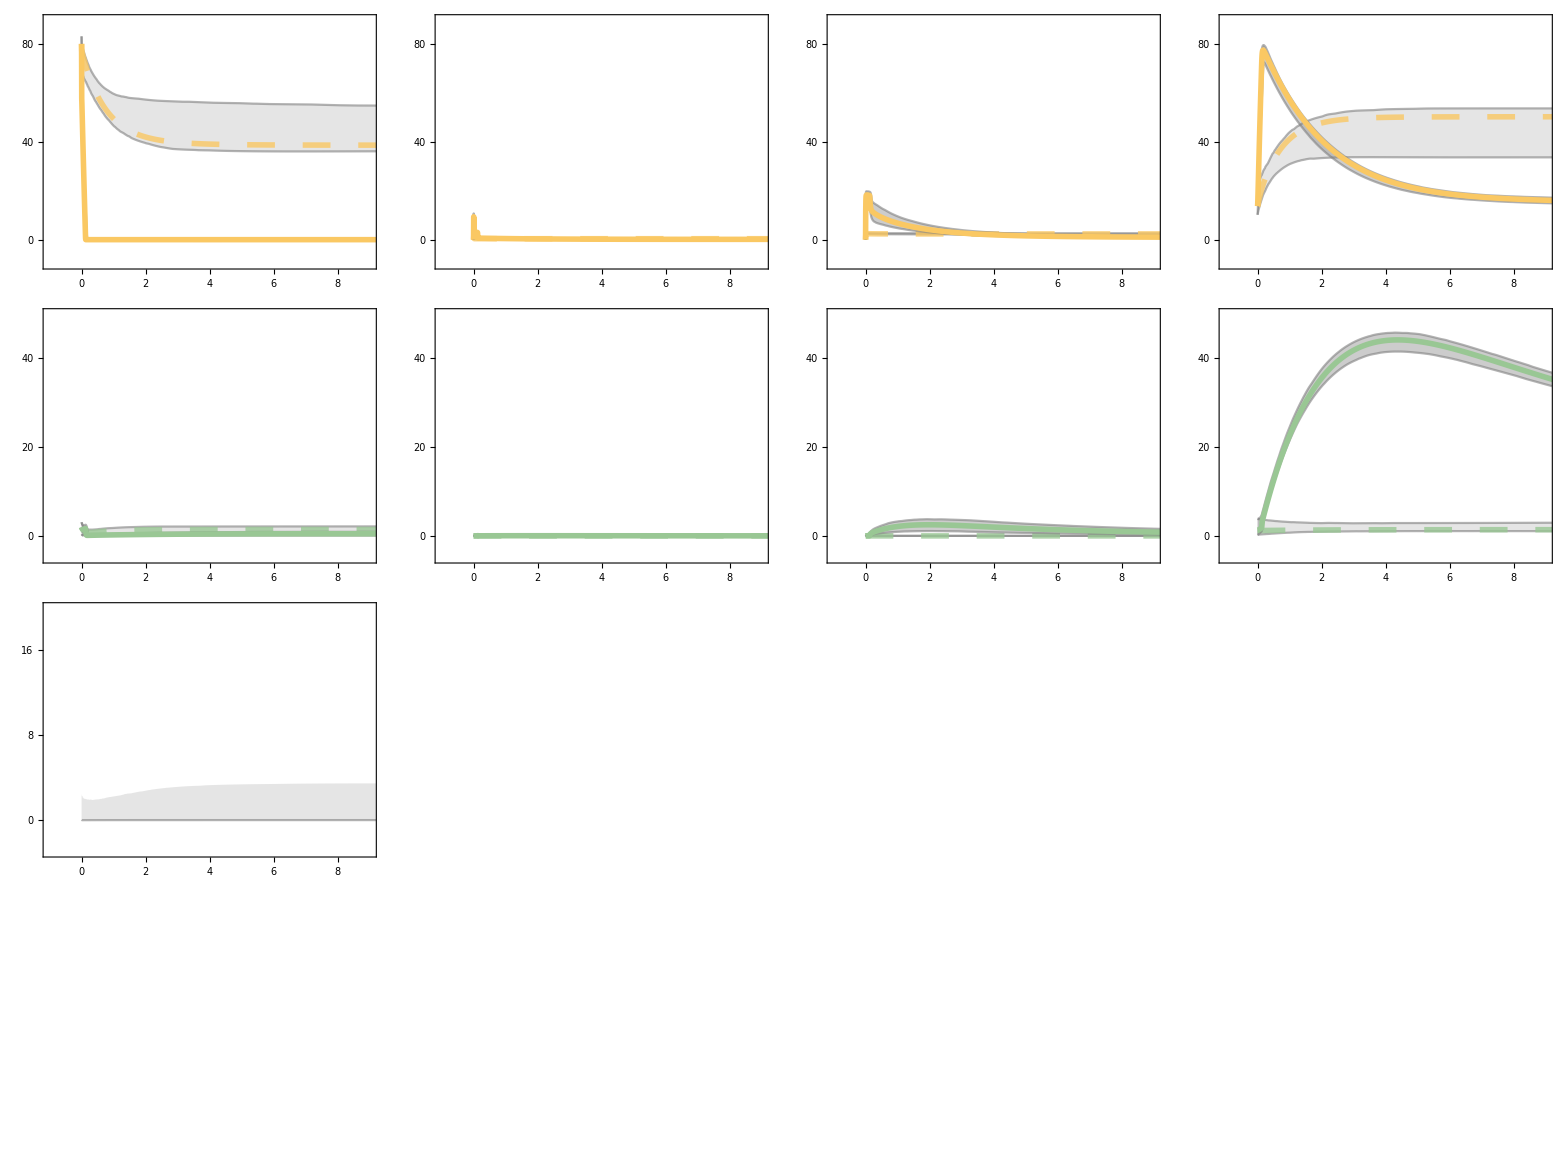

```mathematica
KaiCkinetics=Grid[{
{plot[1,{-10,90},1],plot[2,{-10,90},1],plot[3,{-10,90},1],plot[4,{-10,90},1]},
{plot[5,{-5,50},2,{0,20,40}],plot[6,{-5,50},2,{0,20,40}],plot[7,{-5,50},2,{0,20,40}],plot[8,{-5,50},2,{0,20,40}]},
{plot[9,{-3,20},3,{0,8,16}],plot[10,{-3,20},3,{0,8,16}],plot[11,{-3,20},3,{0,8,16}],plot[12,{-3,20},3,{0,8,16}]},
{plot[13,{-3,20},4,{0,8,16}],plot[14,{-3,20},4,{0,8,16}],plot[15,{-3,20},4,{0,8,16}],plot[16,{-3,20},4,{0,8,16}]}
}]
```

## KaiA phosphorylation state kinetics

```mathematica
time=Range[0,12,0.005];
```

```mathematica
solKaiA[walker_,KaiA_]:=Module[{allSol},
allSol=DoubleGeneralPathConc[walker,1.0,3.5,KaiA,"none",12]⟦{5,6,7,8,13,14,15,16,17}⟧/.t->time;
100/(KaiA/2){allSol⟦1⟧+allSol⟦2⟧,allSol⟦3⟧+allSol⟦4⟧,allSol⟦5⟧+allSol⟦6⟧,allSol⟦7⟧+allSol⟦8⟧,allSol⟦9⟧}
]
```

```mathematica
solKaiABestWalker=solKaiA[bestWalker,1.5];
solsKaiA=Quiet@ParallelTable[Check[solKaiA[walker,1.5],∞],{walker,iterTrajFlat⟦;;;;50⟧}];
solsKaiA=DeleteCases[solsKaiA,∞];
solKaiACI=ParallelTable[{Quantile[solsKaiA⟦All,species,t⟧,0.025],Quantile[solsKaiA⟦All,species,t⟧,1-0.025]},{species,5},{t,Length[solsKaiA⟦1,1⟧]}];
```

```mathematica
solKaiABestWalkerLowA=solKaiA[bestWalker,0.2];
solsKaiALowA=Quiet@ParallelTable[Check[solKaiA[walker,0.2],∞],{walker,iterTrajFlat⟦;;;;50⟧}];
solsKaiALowA=DeleteCases[solsKaiALowA,∞];
solKaiACILowA=ParallelTable[{Quantile[solsKaiALowA⟦All,species,t⟧,0.025],Quantile[solsKaiALowA⟦All,species,t⟧,1-0.025]},{species,5},{t,Length[solsKaiALowA⟦1,1⟧]}];
```

```mathematica
minorFont=30;
majorFont=30;
markerSize=18;
thickness=4;
baseStyle={PlotRange->All,AspectRatio->Full,BaseStyle->FontSize->majorFont,Frame->True,Axes->False,FrameStyle->Directive[Thick,Black],FrameTicksStyle->Thick};

plotKaiA[species_,plotRange_,phosphoform_,ticks_]:=Show[
ListLinePlot[{{time,solKaiACILowA⟦species,All,1⟧}ᵀ,{time,solKaiACILowA⟦species,All,2⟧}ᵀ},PlotRange->{{-1,9},plotRange},baseStyle,FrameTicks->{{ticks,None},{{0,2,4,6,8},None}},ImageSize->{200,200},Filling->{2->{1}},PlotStyle->{{Gray,Opacity[0.6]}},FillingStyle->{Black,Opacity[0.2]}],
ListLinePlot[{time,solKaiABestWalkerLowA⟦species⟧}ᵀ,baseStyle,PlotStyle->{Dashing[0.1],Opacity[0.8],AbsoluteThickness[thickness],UTSDPfColorScheme⟦phosphoform⟧}],

ListLinePlot[{{time,solKaiACI⟦species,All,1⟧}ᵀ,{time,solKaiACI⟦species,All,2⟧}ᵀ},PlotRange->{{-1,9},plotRange},baseStyle,FrameTicks->{{ticks,None},{{0,2,4,6,8},None}},ImageSize->{200,200},Filling->{2->{1}},PlotStyle->{{Gray,Opacity[0.6]}},FillingStyle->{Black,Opacity[0.4]}],
ListLinePlot[{time,solKaiABestWalker⟦species⟧}ᵀ,baseStyle,PlotStyle->{AbsoluteThickness[thickness],UTSDPfColorScheme⟦phosphoform⟧}]
]
```

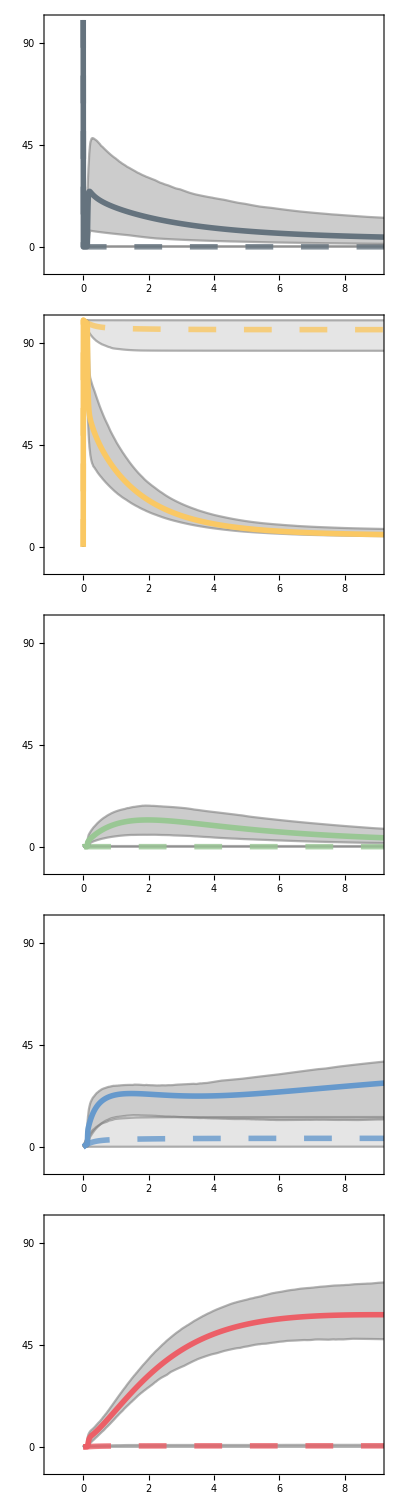

```mathematica
KaiAkinetics=Column[{
plotKaiA[5,{-10,100},-1,{0,45,90}],
plotKaiA[1,{-10,100},1,{0,45,90}],
plotKaiA[2,{-10,100},2,{0,45,90}],
plotKaiA[3,{-10,100},3,{0,45,90}],
plotKaiA[4,{-10,100},4,{0,45,90}]}
]
```

## KaiC dephosphorylation state kinetics

```mathematica
time=Range[0,12,0.005];
```

```mathematica
solDephosFun[walker_]:=Module[{allSol},
allSol=DoubleGeneralDephos[walker,1.0,1.0,3.5,1.5]⟦{1,2,3,4,9,10,11,12}⟧/.t->time
]
```

```mathematica
Clear[solDephos]
```

```mathematica
solDephosBestWalker=solDephosFun[bestWalker];
```

```mathematica
solsDephos=Quiet@Table[Check[solDephosFun[walker],∞],{walker,iterTrajFlat⟦;;;;100⟧}];
```

```mathematica
solsDephos=DeleteCases[solsDephos,∞];
```

```mathematica
solDephosCI=Table[{Quantile[solsDephos⟦All,species,t⟧,0.025],Quantile[solsDephos⟦All,species,t⟧,1-0.025]},{species,8},{t,Length[solsDephos⟦1,1⟧]}];
```

```mathematica
minorFont=30;
majorFont=30;
markerSize=18;
thickness=4;
baseStyle={PlotRange->All,AspectRatio->Full,BaseStyle->FontSize->majorFont,Frame->True,Axes->False,FrameStyle->Directive[Thick,Black],FrameTicksStyle->Thick};

plotDephos[species_,plotRange_,phosphoform_]:=Show[
ListLinePlot[{{time,solDephosCI⟦species,All,1⟧}ᵀ,{time,solDephosCI⟦species,All,2⟧}ᵀ},PlotRange->{{-0.5,12},plotRange},baseStyle,FrameTicks->{{{15,50,85},None},{{1,3,5,7,9,11},None}},ImageSize->{200,200},Filling->{2->{1}},PlotStyle->{{Gray,Opacity[0.6]}},FillingStyle->{Black,Opacity[0.4]}],
ListLinePlot[{time,solDephosBestWalker⟦species⟧}ᵀ,baseStyle,PlotStyle->{AbsoluteThickness[thickness],UTSDPfColorScheme⟦phosphoform⟧}]
]
```

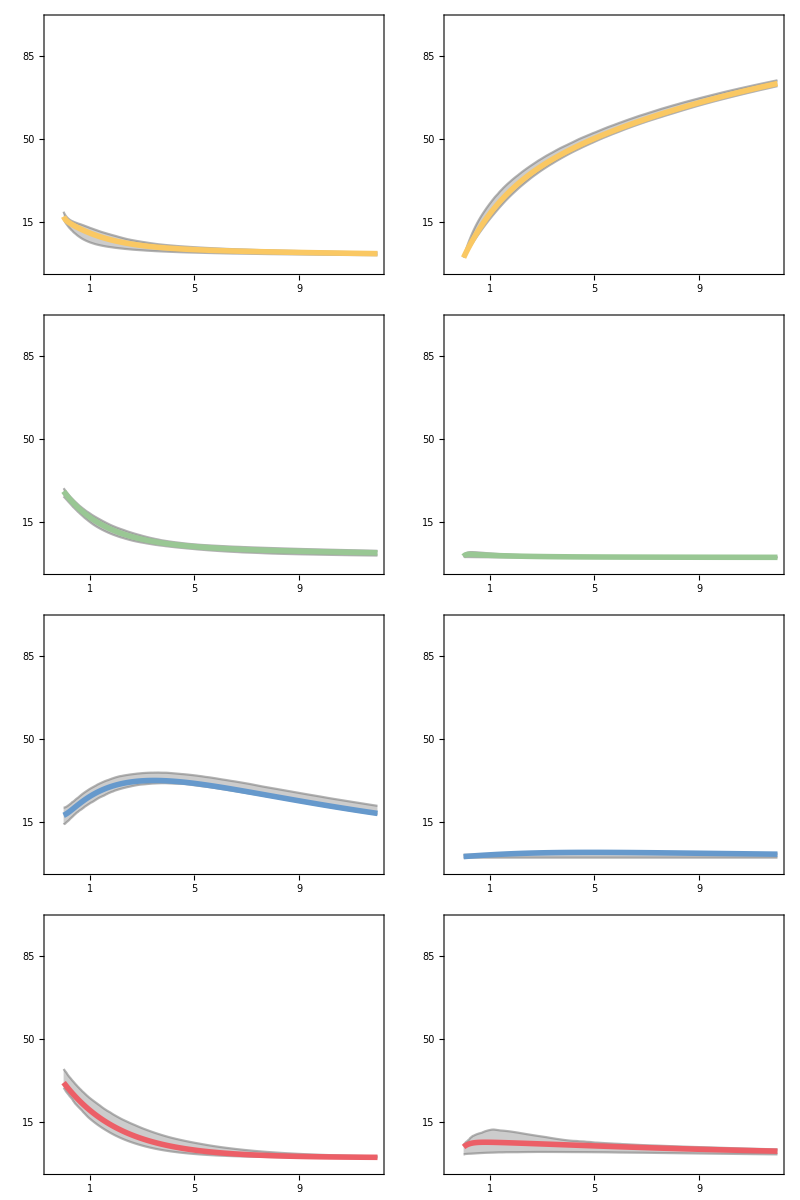

```mathematica
dephosTrajPlt=KaiCDephoskinetics=Grid[{
{plotDephos[1,{-5,100},1],plotDephos[2,{-5,100},1]},
{plotDephos[3,{-5,100},2],plotDephos[4,{-5,100},2]},
{plotDephos[5,{-5,100},3],plotDephos[6,{-5,100},3]},
{plotDephos[7,{-5,100},4],plotDephos[8,{-5,100},4]}
}]
```

## Steady-state KaiC phosphorylation level as a function of ATP/KaiA

```mathematica
percentPhosATPDouble[walker_,ATP_,KaiA_,time_:24]:=Module[{sol},
sol=DoubleGeneral[walker,ATP,3.5,KaiA,time];
Table[Total[sol⟦i⟧],{i,{UKaiC,TKaiC,SKaiC,DKaiC,PKaiC}}]/.t->time
]
```

```mathematica
concHeatMapDouble=ParallelTable[Flatten@{100ATPfrac,KaiA,percentPhosATPDouble[bestWalker,ATPfrac,KaiA]},{ATPfrac,0.05,1.0,0.01},{KaiA,0.2,3,0.02}];
```

```mathematica
concHeatMapDoubleFlat=Flatten[concHeatMapDouble,1];
```

```mathematica
concHeatMapU=concHeatMapDoubleFlat⟦All,{1,2,3}⟧;
concHeatMapT=concHeatMapDoubleFlat⟦All,{1,2,4}⟧;
concHeatMapS=concHeatMapDoubleFlat⟦All,{1,2,5}⟧;
concHeatMapD=concHeatMapDoubleFlat⟦All,{1,2,6}⟧;
concHeatMapP=concHeatMapDoubleFlat⟦All,{1,2,7}⟧;
```

```mathematica
grayLevel=0.35;
majorFont=30;minorFont=30;
Clear[baseStyle]
baseStyle[name_,color_,range_,increment_]:={AspectRatio->1,Frame->{{True,False},{True,False}},ImageSize->450,FrameLabel->{"%ATP","[KaiA] (μM)"},BaseStyle->FontSize->majorFont,FrameStyle->Directive[Thick,Black],FrameTicksStyle->Thick,PlotRange->{{5,100},{0.2,3},{0,100}},ColorFunctionScaling->False,PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->250,LegendLabel->Style[name,FontSize->minorFont,Black,SingleLetterItalics->False],LabelStyle->Directive[FontSize->minorFont,Black]],{1,0.58}],ColorFunction->(Blend[{UTSDPfColorScheme⟦1⟧,UTSDPfColorScheme⟦colorCode⟦color⟧⟧},Rescale[#,{0,range}]]&),Contours->Range[0,range,increment]};

concPContour=ListContourPlot[concHeatMapP,baseStyle["%C^P","P",100,5]];
concTContour=ListContourPlot[concHeatMapT,baseStyle["%C^T","T",25,1.5]];
concSContour=ListContourPlot[concHeatMapS,baseStyle["%C^S","S",30,2]];
concDContour=ListContourPlot[concHeatMapD,baseStyle["%C^D","D",65,5]];
```

```mathematica
Grid[{{concPContour,concTContour,concSContour,concDContour}}]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics-

## KaiA binding affinity plot (ensemble)

```mathematica
Kd[walker_]:=Module[{krT,krD,Kon,kh,ka,kb,kp,kd,dkT,dkD,dkDT,dkhT,dkhS,dkTAD,dkbSDP,dkbDDP,dkbTTP,dkbDTP,dkdSU,dkpTD,dkdDT,dkpSD,dkdATU,dkdADT,dkpAUS,dkDS,dkTD,dkDD,dkhD,dkTAT,dkDAT,dkTAS,dkDAS,dkDAD,dkhAU,dkhAT,dkhAS,dkhAD,dkbUDP,dkbTDP,dkbSTP,dkdDS,dkpASD,dkdADS, dkpAUT, dkpATD,dkdASU,dkaDDP,nucTotal,ATP,ADP,ATPWeighedFrac,kTA,kDA,kT,kD,dkaSTP,dkaTTP,dkaTDP,dkaSDP,dkaUDP,dkaDTP,dkTT,dkTS,dkpUS,Cud,Cut,Csd,Cst,Ctd,Ctt,Cdd,Cdt},

(*Define the free parameters and assign their values*)
{krD,kh,ka,kb,kp,kd,dkhT,dkhS,dkhD,dkTAT,dkTAS,dkTAD,dkhAU,dkhAT,dkhAS,dkhAD,dkaUDP,dkbUDP,dkbTDP,dkbSDP,dkaDDP,dkbDDP,dkbTTP,dkbSTP,dkaDTP,dkbDTP,dkpUS,dkdSU,dkpTD,dkdDT,dkpSD,dkdDS,dkpAUT,dkdATU,dkpATD,dkdADT,dkpASD,dkdADS,dkpAUS,dkdASU}=10^walker⟦1;;nFreePar-1⟧;

Kon=1;
nucTotal=5000.;
ATP=0.5*nucTotal;
ADP=nucTotal-ATP;
ATPWeighedFrac=ATP/(ATP+Kon*ADP);
kTA=krD*ATPWeighedFrac;
dkaSTP=(dkbSTP*dkaDDP*dkdADS)/(dkbDDP*dkpASD);
dkaTTP=(dkbTTP*dkaDDP*dkdADT)/(dkbDDP*dkpATD);
dkaTDP=(dkbTDP*dkpAUT)/dkdATU;
dkaSDP=(dkbSDP*dkpAUS)/dkdASU;

{Cud=(kb dkbUDP)/(ka dkaUDP),
Cut=kb/ka,
Ctd=(kb dkbTDP)/(ka dkaTDP),
Ctt=(kb dkbTTP)/(ka dkaTTP),
Csd= (kb dkbSDP)/(ka dkaSDP),
Cst=(kb dkbSTP)/(ka dkaSTP),
Cdd=(kb dkbDDP)/(ka dkaDDP),
Cdt=(kb dkbDTP)/(ka dkaDTP)}
]
```

```mathematica
{Cud,Cut,Ctd,Ctt,Csd,Cst,Cdd,Cdt}=Kd[bestWalker];
```

```mathematica
affinities=Kd[#]&/@iterTrajFlat;
```

```mathematica
affErrors=Table[{Quantile[affinities⟦All,i⟧,0.025],Quantile[affinities⟦All,i⟧,1-0.025]},{i,8}];
```

```mathematica
Udata=Log[10,affinities⟦All,{1,2}⟧];
Tdata=Log[10,affinities⟦All,{3,4}⟧];
Sdata=Log[10,affinities⟦All,{5,6}⟧];
Ddata=Log[10,affinities⟦All,{7,8}⟧];
```

```mathematica
densityU=SmoothKernelDistribution[Udata,"Oversmooth"];
densityT=SmoothKernelDistribution[Tdata,"Oversmooth"];
densityS=SmoothKernelDistribution[Sdata,"Oversmooth"];
densityD=SmoothKernelDistribution[Ddata,"Oversmooth"];
```

```mathematica
pdfU=PDF[densityU,Udata];
pdfT=PDF[densityT,Tdata];
pdfS=PDF[densityS,Sdata];
pdfD=PDF[densityD,Ddata];
```

```mathematica
confidence={0.68,0.95};
```

```mathematica
contourU=Quantile[pdfU,1-confidence];
contourT=Quantile[pdfT,1-confidence];
contourS=Quantile[pdfS,1-confidence];
contourD=Quantile[pdfD,1-confidence];
```

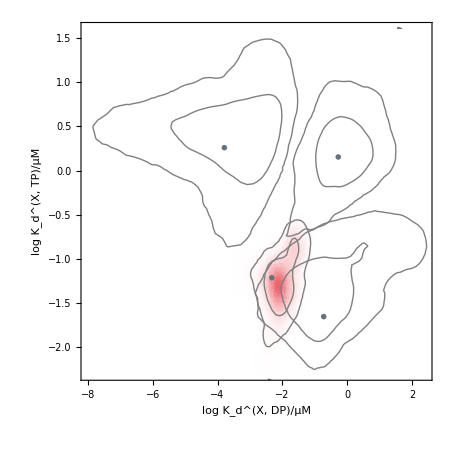

```mathematica
minorFont=35;
majorFont=35;
markerSize=10;
Clear[baseStyle]
baseStyle[color_]:={ImageSize->450,AspectRatio->1,BaseStyle->FontSize->majorFont,Axes->False,Frame->True,FrameStyle->Directive[Thick,Black],FrameTicksStyle->Thick,FrameLabel->{"log K_d^(X, DP)/μM","log K_d^(X, TP)/μM"},PlotRange->{{-8,2.4},{-2.3,1.6},All},Mesh->False,ColorFunction->(Blend[{RGBColor[1,1,1,0],RGBColor[Join[(List@@@UTSDPfColorScheme)⟦colorCode⟦color⟧⟧,{1}]]},#]&)};

{Cud,Cut,Ctd,Ctt,Csd,Cst,Cdd,Cdt}=Kd[bestWalker];

KDplot=Show[
SmoothDensityHistogram[Udata,baseStyle["U"]],
Plot[x,{x,-10,10},PlotStyle->{UTSDPfColorScheme⟦-1⟧,Thickness[0.008],Dashed}],
SmoothDensityHistogram[Tdata,baseStyle["T"]],
SmoothDensityHistogram[Sdata,baseStyle["S"]],
SmoothDensityHistogram[Ddata,baseStyle["D"]],
ListPlot[Log[10,{{Cud,Cut},{Ctd,Ctt},{Csd,Cst},{Cdd,Cdt}}],PlotMarkers->{"*",25},PlotStyle->UTSDPfColorScheme⟦-1⟧],
ContourPlot[PDF[densityU,{x,y}],{x,-8,3},{y,-2,2},Contours->contourU,ContourShading->None,PlotRange->All,ContourStyle->Gray],
ContourPlot[PDF[densityT,{x,y}],{x,-6,3},{y,-2,2},Contours->contourT,ContourShading->None,PlotRange->All,ContourStyle->Gray],
ContourPlot[PDF[densityS,{x,y}],{x,-8,3},{y,-3,2},Contours->contourS,ContourShading->None,PlotRange->All,ContourStyle->Gray],
ContourPlot[PDF[densityD,{x,y}],{x,-8,3},{y,-3,2},Contours->contourD,ContourShading->None,PlotRange->All,ContourStyle->Gray]
]
```

## Steady-state stimulus-response function

```mathematica
ModelPredictionP=ParallelTable[{kaiA,Total[DoubleGeneral[bestWalker,ATPfrac,3.5,kaiA,24]⟦PKaiC⟧/.t->24]},{ATPfrac,{0.25,0.5,1}},{kaiA,0,2,0.01}];
```

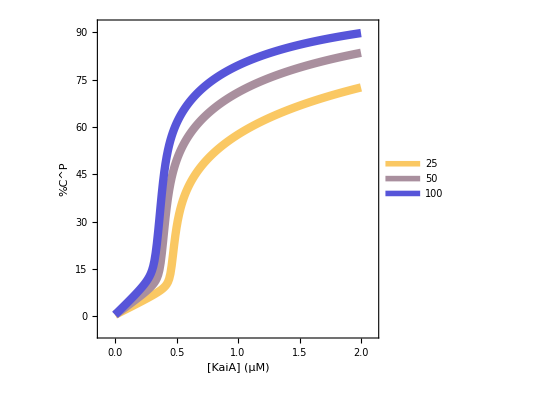

```mathematica
grayLevel=0.35;
minorFont=30;
majorFont=30;
markerSize=20;
markerSize2=30;
thickness=0.015;
baseStyle={ImageSize->400,AspectRatio->1,PlotRange->{{-0.1,2.1},{-5,92}},BaseStyle->FontSize->majorFont,Axes->False,Frame->{{True,False},{True,False}},FrameStyle->Directive[Thick,Black],FrameTicksStyle->Thick,PlotMarkers->{Style[#,FontWeight->Bold]&/@{"□","◦","◇"},ConstantArray[markerSize2,3]}ᵀ};

ModelPredictionPPlt=ListLinePlot[ModelPredictionP,PlotMarkers->None,baseStyle,PlotStyle->{(Blend[{UTSDPfColorScheme⟦1⟧,UTSDPfColorScheme⟦5⟧},#]&/@{0,0.5,1}),Table[Thickness[thickness],{i,3}]}ᵀ,FrameLabel->{"[KaiA] (μM)",Style["%C^P",SingleLetterItalics->False]},
PlotLegends->Placed[LineLegend[Automatic,Style[#,minorFont,Black]&/@{"25","50","100"},Spacings->0.1,LegendMarkerSize->markerSize],{0.85,0.21}]]
```

## Ultrasensitivity quantification

```mathematica
ECcalc[curve_,ϵ_]:=Module[{smoothCurve,τ,Θ,σ,kaiA},
smoothCurve[kaiA_]=Interpolation[curve,kaiA,InterpolationOrder->1];
τ=Quiet[kaiA/.Solve[smoothCurve[kaiA]==ϵ,kaiA]⟦1⟧];
Θ=Quiet[kaiA/.Solve[smoothCurve[kaiA]==1-ϵ,kaiA]⟦1⟧];
σ=Θ-τ;
If[NumberQ[τ]∧NumberQ[σ],{τ,σ},{∞,∞}]
]
```

```mathematica
ultraQuant[walker_,time_]:=Module[{conc,curves,curveP,curveT,curveS,curveD,smoothCurveP,smoothCurveD,smoothCurveT,smoothCurveS,ϵ,kaiA},
ϵ=0.1;
conc=Range[0,2,0.01];
curves=Table[DoubleGeneral[walker,0.25,3.5,kaiA,time],{kaiA,conc}];
curveP=Rescale@Table[Total[curves⟦kaiA,PKaiC⟧]/.t->time,{kaiA,Length[conc]}];
curveD=Rescale@Table[Total[curves⟦kaiA,DKaiC⟧]/.t->time,{kaiA,Length[conc]}];
curveT=Rescale@Table[Total[curves⟦kaiA,TKaiC⟧]/.t->time,{kaiA,Length[conc]}];
curveS=Rescale@Table[Total[curves⟦kaiA,SKaiC⟧]/.t->time,{kaiA,Length[conc]}];
{ECcalc[{conc,curveP}ᵀ,ϵ],ECcalc[{conc,curveD}ᵀ,ϵ],ECcalc[{conc,curveT}ᵀ,ϵ],ECcalc[{conc,curveS}ᵀ,ϵ]}
]
```

```mathematica
ultraPexp={0.5287612986437842,0.9501896401805219};
ultraDexp={0.5731386288022426,1.1339223058167014};
ultraTexp={0.5193873114299746,0.708053295233093};
ultraSexp={0.5001493397387643,0.8310232681208948};
```

```mathematica
ultraBest=ultraQuant[bestWalker,24];
```

Warning: this following calculation is very expensive.

```mathematica
ultraEnsembleWT=ParallelTable[ultraQuant[walker,24],{walker,iterTrajFlat⟦;;;;10⟧}];
```

```mathematica
ultraEnsembleWTDelete=Table[Select[ultraEnsembleWT⟦All,i⟧,0≤#⟦1⟧≤2∧0≤#⟦2⟧≤2&],{i,4}];
```

```mathematica
confidence={0.68,0.95};

densityUltraP=SmoothKernelDistribution[ultraEnsembleWTDelete⟦1⟧,"Oversmooth"];
pdfUltraP=PDF[densityUltraP,ultraEnsembleWTDelete⟦1⟧];
contourUltraP=Quantile[pdfUltraP,1-confidence];

densityUltraD=SmoothKernelDistribution[ultraEnsembleWTDelete⟦2⟧,"Oversmooth"];
pdfUltraD=PDF[densityUltraD,ultraEnsembleWTDelete⟦2⟧];
contourUltraD=Quantile[pdfUltraD,1-confidence];

densityUltraT=SmoothKernelDistribution[ultraEnsembleWTDelete⟦3⟧,"Oversmooth"];
pdfUltraT=PDF[densityUltraT,ultraEnsembleWTDelete⟦3⟧];
contourUltraT=Quantile[pdfUltraT,1-confidence];

densityUltraS=SmoothKernelDistribution[ultraEnsembleWTDelete⟦4⟧,"Oversmooth"];
pdfUltraS=PDF[densityUltraS,ultraEnsembleWTDelete⟦4⟧];
contourUltraS=Quantile[pdfUltraS,1-confidence];
```

```mathematica
minorFont=35;
majorFont=35;
markerSize=10;
Clear[baseStyle]
baseStyle[color_]:={ImageSize->450,AspectRatio->1,BaseStyle->FontSize->majorFont,Axes->False,Frame->True,FrameStyle->Directive[Thick,Black],FrameTicksStyle->Thick,FrameLabel->{"thresholding (μM)","switching (μM)"},Mesh->False,ColorFunction->(Blend[{RGBColor[1,1,1,0],RGBColor[Join[(List@@@UTSDPfColorScheme)⟦colorCode⟦color⟧⟧,{1}]]},#]&)};

ultraEnsemblePPlt=Show[
SmoothDensityHistogram[ultraEnsembleWTDelete⟦1⟧,PlotRange->{{0.,0.8},{0.8,1.6},All},baseStyle["P"]],
ListPlot[{{ultraBest⟦1⟧},{ultraPexp}},PlotMarkers->{"*",25},PlotStyle->{UTSDPfColorScheme⟦-1⟧,UTSDPfColorScheme⟦5⟧}],
ContourPlot[PDF[densityUltraP,{x,y}],{x,0,2},{y,0,2},Contours->contourUltraP,ContourShading->None,PlotRange->All,ContourStyle->Gray],ParametricPlot[{k/9,80k/9},{k,0,1},PlotStyle->{UTSDPfColorScheme⟦-1⟧,Thickness[0.008],Dashed}]
];
ultraEnsembleDPlt=Show[
SmoothDensityHistogram[ultraEnsembleWTDelete⟦2⟧,PlotRange->{{0.,0.8},{0.8,1.6},All},baseStyle["D"]],
ListPlot[{{ultraBest⟦2⟧},{ultraDexp}},PlotMarkers->{"*",25},PlotStyle->{UTSDPfColorScheme⟦-1⟧,UTSDPfColorScheme⟦4⟧}],
ContourPlot[PDF[densityUltraD,{x,y}],{x,0.4,0.6},{y,1.1,1.3},Contours->contourUltraD,ContourShading->None,PlotRange->All,ContourStyle->Gray],
ParametricPlot[{k/9,80k/9},{k,0,1},PlotStyle->{UTSDPfColorScheme⟦-1⟧,Thickness[0.008],Dashed}]
];
ultraEnsembleTPlt=Show[
SmoothDensityHistogram[ultraEnsembleWTDelete⟦3⟧,PlotRange->{{0,0.8},{0.4,1.2},All},baseStyle["T"]],
ListPlot[{{ultraBest⟦3⟧},{ultraTexp}},PlotMarkers->{"*",25},PlotStyle->{UTSDPfColorScheme⟦-1⟧,UTSDPfColorScheme⟦2⟧}],
ContourPlot[PDF[densityUltraT,{x,y}],{x,0,1},{y,0.5,1.5},Contours->contourUltraT,ContourShading->None,PlotRange->All,ContourStyle->Gray],
ParametricPlot[{k/9,80k/9},{k,0,0.5},PlotStyle->{UTSDPfColorScheme⟦-1⟧,Thickness[0.008],Dashed}]
];
ultraEnsembleSPlt=Show[
SmoothDensityHistogram[ultraEnsembleWTDelete⟦4⟧,PlotRange->{{0,0.8},{0.2,1.},All},baseStyle["S"]],
ListPlot[{{ultraBest⟦4⟧},{ultraSexp}},PlotMarkers->{"*",25},PlotStyle->{UTSDPfColorScheme⟦-1⟧,UTSDPfColorScheme⟦3⟧}],
ContourPlot[PDF[densityUltraS,{x,y}],{x,0,1},{y,0,1.5},Contours->contourUltraS,ContourShading->None,PlotRange->All,ContourStyle->Gray],
ParametricPlot[{k/9,80k/9},{k,0,0.5},PlotStyle->{UTSDPfColorScheme⟦-1⟧,Thickness[0.008],Dashed}]
];
```

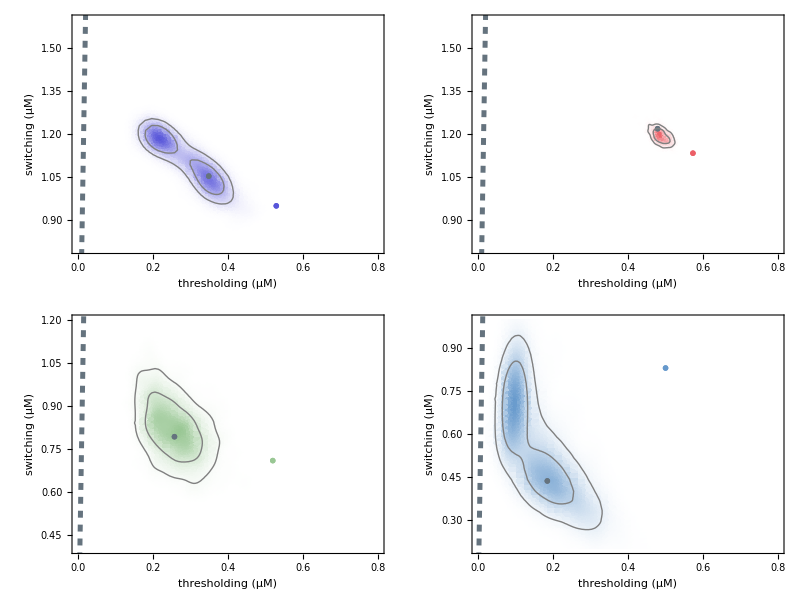

```mathematica
Grid[{{ultraEnsemblePPlt,ultraEnsembleDPlt},{ultraEnsembleTPlt,ultraEnsembleSPlt}}]
```